
-Graphics-
Previous notebook		Content		Next notebook

## 6. Matrix representations

Version (2025-11-28)  The notebook run time is about 25 min on 2020 year laptop (most of time being spent on factorization of determinant identity, not related to calculation of matrix  representation).

### Load main notebook

Load package. WAIT until evaluation of cell is finished to be sure that no errors were produced.

```mathematica
NotebookEvaluate[FileNameJoin[{ParentDirectory[NotebookDirectory[EvaluationNotebook[]]],"GA.nb"}]]
```

### Additional definitions for the notebook

Explicit conjugation function

```mathematica
conjugateExplicit[expr_]:=(expr/.{Complex[x_,y_]:>Complex[x,-y]})
conjugateHermiteConjugate[expr_?MatrixQ]:=(Transpose[expr]/.{Complex[x_,y_]:>Complex[x,-y]})
```

Nice table for representation name and representation matrix

```mathematica
nameAndMatrix[alg_Cl]:=TableForm[Thread[{gaListDefinedElementaryRepresentations[alg],(Row/@(MapAt[MatrixForm,gaDefineMatrixRepresentation[alg,Method->{"TensorProduct","ElementaryRepresentations"->{alg->#}}],{All,2}]&/@gaListDefinedElementaryRepresentations[alg]))}],TableHeadings->{None,{Style["Representation name",Bold],Style["Representation matrices",Bold]}},TableDirections->Column]/;MemberQ[GeometricAlgebra`p`elementaryTPAlgebras,alg]
```

Nice property ∑_i (-𝕖_i^2 x_i^2)^(n/2) =det (∑_i 𝕖_i x_i) of Clifford algebra vectors ant their representation matrix determinants (see Cl[0,3] -> ℍ⊕ℍ subsection for more detailed explanation)

```mathematica
Options[cliffordVectorsDeterminant]={onlyClifford->False};
cliffordVectorsDeterminant[vec_List,algebra:(_Cl|_gaTensorProduct),onlyDifference:(True|False),opts___]:=Module[{cliffordNoMatrixRezult,matrixDetRezult, ortBase=gaOrthonormalBasis[algebra,{1}],theOp=(onlyClifford/.{opts})/.Options[cliffordVectorsDeterminant]},
If[Head[ortBase]===gaOrthonormalBasis, ortBase=gaDefineOrthonormalBasis[algebra,"Grades"->{1}]];cliffordNoMatrixRezult=(-GeometricProduct[#,#]&/@ortBase.(x[#]^2&/@Range[Length[vec]]))^(Dimensions[vec[[1]]][[1]]/2);
If[Not[theOp],
matrixDetRezult=gaDeterminantOfMV[SparseArray[Plus@@Table[vec[[i]]*x[i],{i,Length[vec]}]]];
If[onlyDifference,(cliffordNoMatrixRezult-matrixDetRezult)//Expand,{cliffordNoMatrixRezult//Factor,matrixDetRezult//Factor}],
cliffordNoMatrixRezult]
]/;Length[vec]>0
```

### Introduction

There are implemented two methods for generating matrix representations of Clifford algebras:“TensorProduct”  and “IdealBasis”. The method “IdealBasis” computes primitive idempotent,  left ideal and double sided ideal for matrix  and then generate spinor matrix representation. The method is demonstrated and explained in Spinor notebook. The other method “TensorProduct”, uses iterative procedure and generates higher algebras representations using matrix representations of lower dimensional matrices. All representations are generated from representations of the elementary algebras Cl_(p,q), p+q≤2. In fact after we programmed this method we found its theoretical confirmation in the article of Marchuk (in translation from Russian).

```mathematica
GeometricAlgebra`p`elementaryTPAlgebras//Column
```

Cl[0,0,0]
Cl[0,1,0]
Cl[0,2,0]
Cl[1,0,0]
Cl[1,1,0]
Cl[2,0,0]

using well known Clifford algebra isomorphisms Cl_(1,1)⊗Cl_(p,q)=Cl_(p+1,q+1),  Cl_(0,2)⊗Cl_(p,q)=Cl_(q,p+2), Cl_(2,0)⊗Cl_(p,q)=Cl_(q+2,p). These algebra has the explicit representations, which are included into package code named as

```mathematica
gaListDefinedElementaryRepresentations/@GeometricAlgebra`p`elementaryTPAlgebras//Column
```

{{}}
{Complex,Antisymmetric}
{Pauli[1,2],Pauli[2,3],Pauli[3,1],Trigonometric,TrigonometricAntisymmetric,HyperbolicTrigonometric,HyperbolicTrigonometricAntisymmetric,Real,Q[1,2],Q[2,3],Q[3,1]}
{Diagonal,Symmetric}
{Antisymmetric,SymmetricComplex,Imaginary1,Imaginary2,Trigonometric,TrigonometricAntisymmetric,HyperbolicTrigonometric,HyperbolicTrigonometricAntisymmetric}
{IPauli[1,2],IPauli[2,3],IPauli[3,1],Symmetric,Trigonometric,TrigonometricAntisymmetric,HyperbolicTrigonometric,HyperbolicTrigonometricAntisymmetric}

This can represented more clearly as a table

```mathematica
TableForm[{DisplayForm/@GeometricAlgebra`p`elementaryTPAlgebras,gaListDefinedElementaryRepresentations/@GeometricAlgebra`p`elementaryTPAlgebras},TableHeadings->{{Style["Algebra",Bold],Style["Representation\nname",Bold]},None},TableDirections->Column]
```

Algebra | Cl[0,0,0] | Cl[0,1,0] | Cl[0,2,0] | Cl[1,0,0] | Cl[1,1,0] | Cl[2,0,0]
Representation
name |  | Complex
Antisymmetric | Pauli[1,2]
Pauli[2,3]
Pauli[3,1]
Trigonometric
TrigonometricAntisymmetric
HyperbolicTrigonometric
HyperbolicTrigonometricAntisymmetric
Real
Q[1,2]
Q[2,3]
Q[3,1] | Diagonal
Symmetric | Antisymmetric
SymmetricComplex
Imaginary1
Imaginary2
Trigonometric
TrigonometricAntisymmetric
HyperbolicTrigonometric
HyperbolicTrigonometricAntisymmetric | IPauli[1,2]
IPauli[2,3]
IPauli[3,1]
Symmetric
Trigonometric
TrigonometricAntisymmetric
HyperbolicTrigonometric
HyperbolicTrigonometricAntisymmetric

Each name represents some matrix set, from which higher algebra representations are built.  Algebra representations are constructed with the command gaAlgebraToMatrixRepresentation[algebra,elementary representation names ]. The first argument is the algebra, the second is a list of names of representations of all elementary algebras that are needed for construction.  For example, in the case of elementary algebra Cl_(0,1) representations are either complex 1×1 or real 2×2  matrices

```mathematica
testAlgebra=Cl[0,4];
gaDefineOrthonormalBasis[testAlgebra,"gaNonCommutativeMonomialOrder"->"RevLex"]
```

Basis vectors are stored in   gaOrthonormalBasis[040,RevLex]

Running algebra is: gaRunningAlgebra=  040

{1,1040,2040,12040,3040,13040,23040,123040,4040,14040,24040,124040,34040,134040,234040,1234040}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[testAlgebra,Method->{"IdealBasis","gaPrimitiveIdempotent"->{Automatic,"StartingElement"->{1},"CoefficientDomain"->Reals,Quiet->True,"OutputForm"->"IdempotentFactors"},"gaSemisimpleAlgebraExtensionNonCommutativeMonomialOrder"->"RevLex","gaSemisimpleAlgebraExtension"->"GradeInvertedLast","CoefficientDomain"->Reals},"Grades"->All,"BasisVectorsMultipliers"->Automatic,Quiet->True,"BasisVectorsReordering"->None],{All,2}]
```

{1040→(-1Cl[0,2,0]Quaternion | 0
0 | 1Cl[0,2,0]Quaternion),2040→(-2Cl[0,2,0]Quaternion | 0
0 | 2Cl[0,2,0]Quaternion),3040→(-12Cl[0,2,0]Quaternion | 0
0 | 12Cl[0,2,0]Quaternion),4040→(0 | 1
-1 | 0),12040→(12Cl[0,2,0]Quaternion | 0
0 | 12Cl[0,2,0]Quaternion),13040→(-2Cl[0,2,0]Quaternion | 0
0 | -2Cl[0,2,0]Quaternion),14040→(0 | -1Cl[0,2,0]Quaternion
-1Cl[0,2,0]Quaternion | 0),23040→(1Cl[0,2,0]Quaternion | 0
0 | 1Cl[0,2,0]Quaternion),24040→(0 | -2Cl[0,2,0]Quaternion
-2Cl[0,2,0]Quaternion | 0),34040→(0 | -12Cl[0,2,0]Quaternion
-12Cl[0,2,0]Quaternion | 0),123040→(1 | 0
0 | -1),124040→(0 | 12Cl[0,2,0]Quaternion
-12Cl[0,2,0]Quaternion | 0),134040→(0 | -2Cl[0,2,0]Quaternion
2Cl[0,2,0]Quaternion | 0),234040→(0 | 1Cl[0,2,0]Quaternion
-1Cl[0,2,0]Quaternion | 0),1234040→(0 | 1
1 | 0)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[testAlgebra, Method ->"TensorProduct",Quiet->False],{All,2}]
```

Basis vectors are stored in   gaOrthonormalBasis[200,InvDeg[Lex],{1,2}]

Basis vectors are stored in   gaOrthonormalBasis[020,InvDeg[Lex],{1,2}]

Basis vectors are stored in   gaOrthonormalBasis[200020,InvDeg[Lex],{1}]

{1040→(12020Quaternion | 0
0 | -12020Quaternion),2040→(0 | 12020Quaternion
12020Quaternion | 0),3040→(1020Quaternion | 0
0 | 1020Quaternion),4040→(2020Quaternion | 0
0 | 2020Quaternion),12040→(0 | -1
1 | 0),13040→(2020Quaternion | 0
0 | -2020Quaternion),14040→(-1020Quaternion | 0
0 | 1020Quaternion),23040→(0 | 2020Quaternion
2020Quaternion | 0),24040→(0 | -1020Quaternion
-1020Quaternion | 0),34040→(12020Quaternion | 0
0 | 12020Quaternion),123040→(0 | -1020Quaternion
1020Quaternion | 0),124040→(0 | -2020Quaternion
2020Quaternion | 0),134040→(-1 | 0
0 | 1),234040→(0 | -1
-1 | 0),1234040→(0 | -12020Quaternion
12020Quaternion | 0)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[testAlgebra, Method ->{"TensorProduct","ElementaryRepresentations"->{Cl[0,2]->"Pauli[1,2]",Cl[2,0]-> "IPauli[1,2]",Cl[1,1]->"Antisymmetric",Cl[0,1]->"Complex"},"TargetMatrices"->Complexes},"BasisVectorsMultipliers"->Automatic,Quiet->False],{All,2}]
```

{1040→(0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),2040→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),3040→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),4040→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),12040→(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),13040→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),14040→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ),23040→(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),24040→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),34040→(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),123040→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),124040→(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),134040→(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),234040→(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),1234040→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[testAlgebra, Method ->{"TensorProduct","ElementaryRepresentations"->{Cl[0,2]->"Pauli[1,2]",Cl[2,0]-> "IPauli[1,2]",Cl[1,1]->"Antisymmetric",Cl[0,1]->"Complex"},"TargetMatrices"->Complexes},"BasisVectorsMultipliers"->Automatic,Quiet->False],{All,2}]
```

{1040→(0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),2040→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),3040→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),4040→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),12040→(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),13040→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),14040→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ),23040→(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),24040→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),34040→(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),123040→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),124040→(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),134040→(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),234040→(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),1234040→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0)}

```mathematica
MapAt[MatrixForm,mrep1=gaDefineMatrixRepresentation[testAlgebra, Method ->{"TensorProduct","ElementaryRepresentations"->{Cl[0,2]->"Pauli[1,2]",Cl[2,0]-> "IPauli[1,2]",Cl[1,1]->"Antisymmetric",Cl[0,1]->"Complex"},"BaseVectorAlgebra"->Cl[1,3],"TargetMatrices"->Reals},"BasisVectorsMultipliers"->Automatic,Quiet->True],{All,2}]
```

Basis vectors are stored in   gaOrthonormalBasis[110,InvDeg[Lex],{1,2}]

Basis vectors are stored in   gaOrthonormalBasis[020110,InvDeg[Lex],{1}]

{1040→(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),2040→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),3040→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),4040→(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),12040→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),13040→(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),14040→(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),23040→(0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),24040→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ),34040→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),123040→(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),124040→(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),134040→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),234040→(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),1234040→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[testAlgebra, Method ->{"TensorProduct","ElementaryRepresentations"->{Cl[0,2]->"Pauli[1,2]",Cl[2,0]-> "IPauli[1,2]",Cl[1,1]->"Antisymmetric",Cl[0,1]->"Complex"},"BaseVectorAlgebra"->Cl[3,1],"TargetMatrices"->Reals},"BasisVectorsMultipliers"->Automatic,Quiet->True],{All,2}]
```

Basis vectors are stored in   gaOrthonormalBasis[200110,InvDeg[Lex],{1}]

{1040→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),2040→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),3040→(0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),4040→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),12040→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),13040→(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),14040→(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),23040→(-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),24040→(0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),34040→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),123040→(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),124040→(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),134040→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),234040→(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),1234040→(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)}

```mathematica
gaDefineMatrixRepresentation[Cl[0,1]]
```

Basis vectors are stored in   gaOrthonormalBasis[010,InvDeg[Lex],{1}]

{1010→{{0,1},{-1,0}}}

```mathematica
gaDefineMatrixRepresentation[Cl[0,1],Method->{"TensorProduct","ElementaryRepresentations"->{Cl[0,1]->"Complex"}},"BasisVectorsMultipliers"->{-1}]
```

{1010→{{-ⅈ}}}

```mathematica
MatrixForm/@gaDefineMatrixRepresentation[Cl[0,1],Method->{"TensorProduct","ElementaryRepresentations"->{Cl[0,1]->#}}]&/@gaListDefinedElementaryRepresentations[Cl[0,1]]
```

{{1010→{{ⅈ}}},{1010→{{0,1},{-1,0}}}}

Representations can be symbolic as well, however calculations with symbolic matrices is largely untested. For example, Cl_(0,2) representation names are

```mathematica
(repCl02=gaListDefinedElementaryRepresentations[Cl[0,2]])//Column
```

Pauli[1,2]
Pauli[2,3]
Pauli[3,1]
Trigonometric
TrigonometricAntisymmetric
HyperbolicTrigonometric
HyperbolicTrigonometricAntisymmetric
Real
Q[1,2]
Q[2,3]
Q[3,1]

Their corresponding matrix representations  are

```mathematica
(MapAt[MatrixForm,gaDefineMatrixRepresentation[Cl[0,2],Method->{"TensorProduct","ElementaryRepresentations"->{Cl[0,2]->#}},"BasisVectorsMultipliers"->Automatic],{All,2}]&/@repCl02)//Column
```

{1020→(ⅈ | 0
0 | -ⅈ),2020→(0 | 1
-1 | 0),12020→(0 | ⅈ
ⅈ | 0)}
{1020→(0 | 1
-1 | 0),2020→(0 | ⅈ
ⅈ | 0),12020→(ⅈ | 0
0 | -ⅈ)}
{1020→(0 | ⅈ
ⅈ | 0),2020→(ⅈ | 0
0 | -ⅈ),12020→(0 | 1
-1 | 0)}
{1020→(-ⅈ Sin[φ$13057] | -ⅈ Cos[φ$13057]
-ⅈ Cos[φ$13057] | ⅈ Sin[φ$13057]),2020→(ⅈ Cos[φ$13057] | -ⅈ Sin[φ$13057]
-ⅈ Sin[φ$13057] | -ⅈ Cos[φ$13057]),12020→(0 | -Cos[φ$13057]^2-Sin[φ$13057]^2
Cos[φ$13057]^2+Sin[φ$13057]^2 | 0)}
{1020→(-ⅈ Sin[φ$13077] | -Cos[φ$13077]
Cos[φ$13077] | ⅈ Sin[φ$13077]),2020→(-ⅈ Cos[φ$13077] | Sin[φ$13077]
-Sin[φ$13077] | ⅈ Cos[φ$13077]),12020→(0 | -ⅈ Cos[φ$13077]^2-ⅈ Sin[φ$13077]^2
-ⅈ Cos[φ$13077]^2-ⅈ Sin[φ$13077]^2 | 0)}
{1020→(-Sinh[φ$13097] | -ⅈ Cosh[φ$13097]
-ⅈ Cosh[φ$13097] | Sinh[φ$13097]),2020→(-ⅈ Cosh[φ$13097] | Sinh[φ$13097]
Sinh[φ$13097] | ⅈ Cosh[φ$13097]),12020→(0 | Cosh[φ$13097]^2-Sinh[φ$13097]^2
-Cosh[φ$13097]^2+Sinh[φ$13097]^2 | 0)}
{1020→(Sinh[φ$13117] | -Cosh[φ$13117]
Cosh[φ$13117] | -Sinh[φ$13117]),2020→(ⅈ Cosh[φ$13117] | -ⅈ Sinh[φ$13117]
ⅈ Sinh[φ$13117] | -ⅈ Cosh[φ$13117]),12020→(0 | ⅈ Cosh[φ$13117]^2-ⅈ Sinh[φ$13117]^2
ⅈ Cosh[φ$13117]^2-ⅈ Sinh[φ$13117]^2 | 0)}
{1020→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),2020→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),12020→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)}
{1020→(1020Quaternion),2020→(2020Quaternion),12020→(12020Quaternion)}
{1020→(2020Quaternion),2020→(12020Quaternion),12020→(1020Quaternion)}
{1020→(12020Quaternion),2020→(1020Quaternion),12020→(2020Quaternion)}

Which can be more clearly seen from the table

```mathematica
nameAndMatrix[Cl[0,2]]
```

Representation name | Representation matrices
Pauli[1,2] | 1020→(ⅈ | 0
0 | -ⅈ)2020→(0 | 1
-1 | 0)12020→(0 | ⅈ
ⅈ | 0)
Pauli[2,3] | 1020→(0 | 1
-1 | 0)2020→(0 | ⅈ
ⅈ | 0)12020→(ⅈ | 0
0 | -ⅈ)
Pauli[3,1] | 1020→(0 | ⅈ
ⅈ | 0)2020→(ⅈ | 0
0 | -ⅈ)12020→(0 | 1
-1 | 0)
Trigonometric | 1020→(-ⅈ Sin[φ$13336] | -ⅈ Cos[φ$13336]
-ⅈ Cos[φ$13336] | ⅈ Sin[φ$13336])2020→(ⅈ Cos[φ$13336] | -ⅈ Sin[φ$13336]
-ⅈ Sin[φ$13336] | -ⅈ Cos[φ$13336])12020→(0 | -Cos[φ$13336]^2-Sin[φ$13336]^2
Cos[φ$13336]^2+Sin[φ$13336]^2 | 0)
TrigonometricAntisymmetric | 1020→(-ⅈ Sin[φ$13353] | -Cos[φ$13353]
Cos[φ$13353] | ⅈ Sin[φ$13353])2020→(-ⅈ Cos[φ$13353] | Sin[φ$13353]
-Sin[φ$13353] | ⅈ Cos[φ$13353])12020→(0 | -ⅈ Cos[φ$13353]^2-ⅈ Sin[φ$13353]^2
-ⅈ Cos[φ$13353]^2-ⅈ Sin[φ$13353]^2 | 0)
HyperbolicTrigonometric | 1020→(-Sinh[φ$13370] | -ⅈ Cosh[φ$13370]
-ⅈ Cosh[φ$13370] | Sinh[φ$13370])2020→(-ⅈ Cosh[φ$13370] | Sinh[φ$13370]
Sinh[φ$13370] | ⅈ Cosh[φ$13370])12020→(0 | Cosh[φ$13370]^2-Sinh[φ$13370]^2
-Cosh[φ$13370]^2+Sinh[φ$13370]^2 | 0)
HyperbolicTrigonometricAntisymmetric | 1020→(Sinh[φ$13387] | -Cosh[φ$13387]
Cosh[φ$13387] | -Sinh[φ$13387])2020→(ⅈ Cosh[φ$13387] | -ⅈ Sinh[φ$13387]
ⅈ Sinh[φ$13387] | -ⅈ Cosh[φ$13387])12020→(0 | ⅈ Cosh[φ$13387]^2-ⅈ Sinh[φ$13387]^2
ⅈ Cosh[φ$13387]^2-ⅈ Sinh[φ$13387]^2 | 0)
Real | 1020→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0)2020→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)12020→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)
Q[1,2] | 1020→(1020Quaternion)2020→(2020Quaternion)12020→(12020Quaternion)
Q[2,3] | 1020→(2020Quaternion)2020→(12020Quaternion)12020→(1020Quaternion)
Q[3,1] | 1020→(12020Quaternion)2020→(1020Quaternion)12020→(2020Quaternion)

First three are pairs of Pauli matrices, then follow representations of symbolic 2×2 matrices, the real 4×4 representation and three quaternionic representations. For convenience we provide default elementary representations for all Clifford algebras up to Cl_(8,8) (full periodicity table). For example,

```mathematica
gaDefineOrthonormalBasis[Cl[0,3],"gaNonCommutativeMonomialOrder" -> "RevLex"]
```

Basis vectors are stored in   gaOrthonormalBasis[030,RevLex]

Running algebra is: gaRunningAlgebra=  030

{1,1030,2030,12030,3030,13030,23030,123030}

```mathematica
{gaRunningAlgebra,gaRunningOrdering}
```

{030,RevLex}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[Cl[0,3],Method->"IdealBasis"],{All,2}]
```

Expected number of idempotents is   1

Blades, which square to 1 are   {123030}

Full system of commuting blades are  {123030}

The primitive idempotent is   1/2 (1+123030)

gaLeftIdeal::NotSimpleAlgebra: The algebra 0 is not simple. Only half of left ideal will be generated.

The sort order is   RevLex

The sorted bilateral ideal is   {1/2+1/2 123030,1030/2-23030/2,2030/2+13030/2,3030/2-12030/2}

gaLeftIdeal::NotSimpleAlgebra: The algebra 0 is not simple. Only half of left ideal will be generated.

The sort order is   RevLex

The sorted left minimal ideal is   {3030/2-12030/2}

{1030→(-1020Quaternion | 0
0 | 1020Quaternion),2030→(-2020Quaternion | 0
0 | 2020Quaternion),3030→(-12020Quaternion | 0
0 | 12020Quaternion),12030→(12020Quaternion | 0
0 | 12020Quaternion),13030→(-2020Quaternion | 0
0 | -2020Quaternion),23030→(1020Quaternion | 0
0 | 1020Quaternion),123030→(1 | 0
0 | -1)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[Cl[0,3],Method->"TensorProduct"],{All,2}]
```

Basis vectors are stored in   gaOrthonormalBasis[100,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[100020,InvDeg[Lex],{1}]

{1030→(12020Quaternion | 0
0 | -12020Quaternion),2030→(1020Quaternion | 0
0 | 1020Quaternion),3030→(2020Quaternion | 0
0 | 2020Quaternion),12030→(2020Quaternion | 0
0 | -2020Quaternion),13030→(-1020Quaternion | 0
0 | 1020Quaternion),23030→(12020Quaternion | 0
0 | 12020Quaternion),123030→(-1 | 0
0 | 1)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[Cl[0,3],Method->{"TensorProduct"},"BasisVectorsReordering"->{2,3,1}],{All,2}]
```

{1030→(1020Quaternion | 0
0 | 1020Quaternion),2030→(2020Quaternion | 0
0 | 2020Quaternion),3030→(12020Quaternion | 0
0 | -12020Quaternion),12030→(12020Quaternion | 0
0 | 12020Quaternion),13030→(-2020Quaternion | 0
0 | 2020Quaternion),23030→(1020Quaternion | 0
0 | -1020Quaternion),123030→(-1 | 0
0 | 1)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[Cl[1,3],Method->{"TensorProduct"}],{All,2}]
```

Basis vectors are stored in   gaOrthonormalBasis[130,InvDeg[Lex],{1}]

{1130→(1 | 0
0 | -1),2130→(0 | 1020Quaternion
1020Quaternion | 0),3130→(0 | 2020Quaternion
2020Quaternion | 0),4130→(0 | 1
-1 | 0),12130→(0 | 1020Quaternion
-1020Quaternion | 0),13130→(0 | 2020Quaternion
-2020Quaternion | 0),14130→(0 | 1
1 | 0),23130→(12020Quaternion | 0
0 | 12020Quaternion),24130→(-1020Quaternion | 0
0 | 1020Quaternion),34130→(-2020Quaternion | 0
0 | 2020Quaternion),123130→(12020Quaternion | 0
0 | -12020Quaternion),124130→(-1020Quaternion | 0
0 | -1020Quaternion),134130→(-2020Quaternion | 0
0 | -2020Quaternion),234130→(0 | 12020Quaternion
-12020Quaternion | 0),1234130→(0 | 12020Quaternion
12020Quaternion | 0)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[Cl[0,3],Method->{"TensorProduct","ElementaryRepresentations"->{Cl[0,1]->"Complex",Cl[1,0]->"Diagonal",Cl[1,1]->"Antisymmetric",Cl[2,0]->"Symmetric",Cl[0,2]->{"Q[2,3]"}}}],{All,2}]
```

{1030→(1020Quaternion | 0
0 | -1020Quaternion),2030→(2020Quaternion | 0
0 | 2020Quaternion),3030→(12020Quaternion | 0
0 | 12020Quaternion),12030→(12020Quaternion | 0
0 | -12020Quaternion),13030→(-2020Quaternion | 0
0 | 2020Quaternion),23030→(1020Quaternion | 0
0 | 1020Quaternion),123030→(-1 | 0
0 | 1)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[Cl[0,4],Method->{"IdealBasis","gaPrimitiveIdempotent"->{Automatic,"StartingElement"->{1},"OutputForm"->"IdempotentFactors","NumberOfPrimitiveFactors"->Automatic,Quiet->True},"gaIdempotentAndLeftIdealBasisAndDoubleSidedIdealWithReplacementRules"->{},"gaNonCommutativeMonomialOrder"->"RevLex","gaSemisimpleAlgebraExtensionNonCommutativeMonomialOrder"->"InvLex","gaSemisimpleAlgebraExtension"->"GradeInvertedLast","CoefficientDomain"->Reals},Quiet->True],{All,2}]
```

{1040→(-1020Quaternion | 0
0 | 1020Quaternion),2040→(-2020Quaternion | 0
0 | 2020Quaternion),3040→(-12020Quaternion | 0
0 | 12020Quaternion),4040→(0 | 1
-1 | 0),12040→(12020Quaternion | 0
0 | 12020Quaternion),13040→(-2020Quaternion | 0
0 | -2020Quaternion),14040→(0 | -1020Quaternion
-1020Quaternion | 0),23040→(1020Quaternion | 0
0 | 1020Quaternion),24040→(0 | -2020Quaternion
-2020Quaternion | 0),34040→(0 | -12020Quaternion
-12020Quaternion | 0),123040→(1 | 0
0 | -1),124040→(0 | 12020Quaternion
-12020Quaternion | 0),134040→(0 | -2020Quaternion
2020Quaternion | 0),234040→(0 | 1020Quaternion
-1020Quaternion | 0),1234040→(0 | 1
1 | 0)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[Cl[0,2]],{All,2}]
```

{1020→(1020Quaternion),2020→(2020Quaternion),12020→(12020Quaternion)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[Cl[0,2],Method->{"TensorProduct","ElementaryRepresentations"->{Cl[0,1]->"Complex",Cl[1,0]->"Diagonal",Cl[1,1]->"Antisymmetric",Cl[2,0]->"Symmetric",Cl[0,2]->{"Pauli[1,2]"}}}],{All,2}]
```

{1020→(ⅈ | 0
0 | -ⅈ),2020→(0 | 1
-1 | 0),12020→(0 | ⅈ
ⅈ | 0)}

### Few examples

Before calculating representations of full periodicity table (and large algebras) it is useful to give some usage examples

#### Associated Pauli matrices

Associated Pauli matrices τ1,τ2,τ3 can be easily obtained from Pauli spin matrices

```mathematica
gaDefineOrthonormalBasis[Cl[0,2]];
```

Running algebra is: gaRunningAlgebra=  020

```mathematica
MapAt[MatrixForm,PauliAssociatedVectors=gaDefineMatrixRepresentation[Cl[0,2],Method->{"TensorProduct","ElementaryRepresentations"->{Cl[0,2]->"Pauli[3,1]"},"TargetMatrices"->Reals}],{All,2}]
```

{1020→(0 | ⅈ
ⅈ | 0),2020→(ⅈ | 0
0 | -ⅈ),12020→(0 | 1
-1 | 0)}

We only need to properly order the result

```mathematica
MatrixForm/@({τ0,τ1,τ3,τ2}=Prepend[{𝕖[1],𝕖[2],𝕖[1,2]}/.PauliAssociatedVectors,IdentityMatrix[2]])
```

{(1 | 0
0 | 1),(0 | ⅈ
ⅈ | 0),(ⅈ | 0
0 | -ⅈ),(0 | 1
-1 | 0)}

The below listed matrices are standard associated (i.e. two matrices are complex instead of one) Pauli matrices

```mathematica
MatrixForm/@{τ1,τ2,τ3}
```

{(0 | ⅈ
ⅈ | 0),(0 | 1
-1 | 0),(ⅈ | 0
0 | -ⅈ)}

Contrary to Pauli spin matrices{(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1)}, two of associated Pauli matrices are complex and one is real.

#### Pauli spin matrices

Of course, Pauli spin matrices can be obtained from associated Pauli matrices by simple multiplication by (-I)

```mathematica
MatrixForm/@((-I){τ1,τ2,τ3})
```

{(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1)}

However in order to show more commands we explicitly obtain Pauli spin matrices from Cl_(3,0) representation. In order to write representation of  Cl_(3,0) first let’s look how this algebra factorizes into above listed elementary representations

```mathematica
gaToTensorProduct[Cl[3,0]]
```

010200

Thought the factorization preference can be influenced by option

```mathematica
Options[gaToTensorProduct]
```

{ReductionOrder→{{110},{200,020}}}

which means, that first we try to factor Cl_(1,1)part and only then Cl_(2,0) and Cl_(0,2) algebras (representations of which are a bit more complicated). In this case, however, the result is uniquely determined, so we have no freedom of chose.

We see that Cl_(3,0) can be written as a direct product of algebras Cl_(0,1) and Cl_(2,0). Then in order to get representation of Cl_(3,0) we can use any combination of representations of these elementary algebras

```mathematica
gaListDefinedElementaryRepresentations[Cl[0,1]]
```

{Complex,Antisymmetric}

```mathematica
nameAndMatrix[Cl[0,1]]
```

Representation name | Representation matrices
Complex | 1010→(ⅈ)
Antisymmetric | 1010→(0 | 1
-1 | 0)

It is clear, that in order to get  2×2 matrices, the representation of Cl_(0,1) should be one dimensional (i.e. simply imaginary unit).

```mathematica
gaDefineMatrixRepresentation[Cl[0,1],Method->{"TensorProduct","ElementaryRepresentations"->{Cl[0,1]->"Complex"},"TargetMatrices"->Reals}]
```

{1010→{{ⅈ}}}

As far as concerns Cl_(2,0),

```mathematica
gaListDefinedElementaryRepresentations[Cl[2,0]]
```

{IPauli[1,2],IPauli[2,3],IPauli[3,1],Symmetric,Trigonometric,TrigonometricAntisymmetric,HyperbolicTrigonometric,HyperbolicTrigonometricAntisymmetric}

```mathematica
nameAndMatrix[Cl[2,0]]
```

Representation name | Representation matrices
IPauli[1,2] | 1200→(-1 | 0
0 | 1)2200→(0 | ⅈ
-ⅈ | 0)12200→(0 | -ⅈ
-ⅈ | 0)
IPauli[2,3] | 1200→(0 | ⅈ
-ⅈ | 0)2200→(0 | -1
-1 | 0)12200→(-ⅈ | 0
0 | ⅈ)
IPauli[3,1] | 1200→(0 | -1
-1 | 0)2200→(-1 | 0
0 | 1)12200→(0 | -1
1 | 0)
Symmetric | 1200→(1 | 0
0 | -1)2200→(0 | 1
1 | 0)12200→(0 | 1
-1 | 0)
Trigonometric | 1200→(Sin[φ$17577] | Cos[φ$17577]
Cos[φ$17577] | -Sin[φ$17577])2200→(-Cos[φ$17577] | Sin[φ$17577]
Sin[φ$17577] | Cos[φ$17577])12200→(0 | Cos[φ$17577]^2+Sin[φ$17577]^2
-Cos[φ$17577]^2-Sin[φ$17577]^2 | 0)
TrigonometricAntisymmetric | 1200→(-Cos[φ$17594] | -ⅈ Sin[φ$17594]
ⅈ Sin[φ$17594] | Cos[φ$17594])2200→(-Sin[φ$17594] | ⅈ Cos[φ$17594]
-ⅈ Cos[φ$17594] | Sin[φ$17594])12200→(0 | -ⅈ Cos[φ$17594]^2-ⅈ Sin[φ$17594]^2
-ⅈ Cos[φ$17594]^2-ⅈ Sin[φ$17594]^2 | 0)
HyperbolicTrigonometric | 1200→(-ⅈ Sinh[φ$17611] | Cosh[φ$17611]
Cosh[φ$17611] | ⅈ Sinh[φ$17611])2200→(Cosh[φ$17611] | ⅈ Sinh[φ$17611]
ⅈ Sinh[φ$17611] | -Cosh[φ$17611])12200→(0 | -Cosh[φ$17611]^2+Sinh[φ$17611]^2
Cosh[φ$17611]^2-Sinh[φ$17611]^2 | 0)
HyperbolicTrigonometricAntisymmetric | 1200→(Cosh[φ$17628] | -Sinh[φ$17628]
Sinh[φ$17628] | -Cosh[φ$17628])2200→(-ⅈ Sinh[φ$17628] | ⅈ Cosh[φ$17628]
-ⅈ Cosh[φ$17628] | ⅈ Sinh[φ$17628])12200→(0 | ⅈ Cosh[φ$17628]^2-ⅈ Sinh[φ$17628]^2
ⅈ Cosh[φ$17628]^2-ⅈ Sinh[φ$17628]^2 | 0)

we can choose, for example

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[Cl[2,0],Method->{"TensorProduct","ElementaryRepresentations"->{Cl[2,0]->"IPauli[1,2]"}}],{All,2}]
```

{1200→(-1 | 0
0 | 1),2200→(0 | ⅈ
-ⅈ | 0),12200→(0 | -ⅈ
-ⅈ | 0)}

Then Pauli matrices represents Cl_(3,0) vectors

```mathematica
MapAt[MatrixForm,(PauliSpinVectors=gaDefineMatrixRepresentation[Cl[3,0],Method->{"TensorProduct","ElementaryRepresentations"->{Cl[0,1]->"Complex",Cl[2,0]->"IPauli[1,2]"}},"BasisVectorsMultipliers"->{{1},{-1,-1}},"BasisVectorsReordering"->{1,3,2},"Grades"->{1}]),{All,2}]
```

Basis vectors are stored in   gaOrthonormalBasis[010200,InvDeg[Lex],{1}]

Basis vectors are stored in   gaOrthonormalBasis[300,InvDeg[Lex],{1}]

{1300→(0 | 1
1 | 0),2300→(0 | -ⅈ
ⅈ | 0),3300→(1 | 0
0 | -1)}

Usually they are ordered in the following order: {(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1)}

The entire  Cl_(3,0) algebra matrix representation then can be obtained as

```mathematica
MapAt[MatrixForm,fullMatrixBase[Cl[3,0]]=Prepend[gaDefineMatrixRepresentation[PauliSpinVectors],1->IdentityMatrix[2]],{All,2}]
```

{1→(1 | 0
0 | 1),1300→(0 | 1
1 | 0),2300→(0 | -ⅈ
ⅈ | 0),3300→(1 | 0
0 | -1),12300→(ⅈ | 0
0 | -ⅈ),13300→(0 | -1
1 | 0),23300→(0 | ⅈ
ⅈ | 0),123300→(ⅈ | 0
0 | ⅈ)}

Now let’s compare multiplication tables of  Cl_(3,0) algebra orthonormal base and just obtained matrix representation. Orthonormal base is easy to obtain

```mathematica
fullSymbolicBase[Cl[3,0]]=gaDefineOrthonormalBasis[Cl[3,0]]
```

Running algebra is: gaRunningAlgebra=  300

{1,1300,2300,3300,12300,13300,23300,123300}

The multiplication table then is

```mathematica
TableForm[
symbolicTable=Outer[GeometricProduct,fullSymbolicBase[Cl[3,0]],fullSymbolicBase[Cl[3,0]]],TableHeadings->{fullSymbolicBase[Cl[3,0]],fullSymbolicBase[Cl[3,0]]}]
```

| 1 | 1300 | 2300 | 3300 | 12300 | 13300 | 23300 | 123300
1 | 1 | 1300 | 2300 | 3300 | 12300 | 13300 | 23300 | 123300
1300 | 1300 | 1 | 12300 | 13300 | 2300 | 3300 | 123300 | 23300
2300 | 2300 | -12300 | 1 | 23300 | -1300 | -123300 | 3300 | -13300
3300 | 3300 | -13300 | -23300 | 1 | 123300 | -1300 | -2300 | 12300
12300 | 12300 | -2300 | 1300 | 123300 | -1 | -23300 | 13300 | -3300
13300 | 13300 | -3300 | -123300 | 1300 | 23300 | -1 | -12300 | 2300
23300 | 23300 | 123300 | -3300 | 2300 | -13300 | 12300 | -1 | -1300
123300 | 123300 | 23300 | -13300 | 12300 | -3300 | 2300 | -1300 | -1

In order to make comparison we have to make substitution rules. Note, that we explicitly added substitutions for negative elements as well

```mathematica
symbolicBaseToMatrixBaseRules=Flatten[Append[{#},#/.{Rule[a_,b_]:>Rule[-a,-b]}]&/@fullMatrixBase[Cl[3,0]]]
```

{1→{{1,0},{0,1}},-1→{{-1,0},{0,-1}},1300→{{0,1},{1,0}},-1300→{{0,-1},{-1,0}},2300→{{0,-ⅈ},{ⅈ,0}},-2300→{{0,ⅈ},{-ⅈ,0}},3300→{{1,0},{0,-1}},-3300→{{-1,0},{0,1}},12300→{{ⅈ,0},{0,-ⅈ}},-12300→{{-ⅈ,0},{0,ⅈ}},13300→{{0,-1},{1,0}},-13300→{{0,1},{-1,0}},23300→{{0,ⅈ},{ⅈ,0}},-23300→{{0,-ⅈ},{-ⅈ,0}},123300→{{ⅈ,0},{0,ⅈ}},-123300→{{-ⅈ,0},{0,-ⅈ}}}

Then using these substitution rules we replace elements in symbolicTable by matrices and subtract table explicitly obtained from fullMatrixBase[Cl[3,0]]

```mathematica
MatrixForm/@Flatten[((symbolicTable/.symbolicBaseToMatrixBaseRules)-Outer[Dot,Unevaluated/@(Last/@fullMatrixBase[Cl[3,0]]),Unevaluated/@(Last/@fullMatrixBase[Cl[3,0]])]),1]
```

{(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0)}

It is easy to see, that subtraction gives all zero matrices, meaning that both multiplication tables exactly coincides. An alternative way using “IdealBasis” method

```mathematica
MapAt[MatrixForm,PauliSpinVectors,{All,2}]
```

{1300→(0 | 1
1 | 0),2300→(0 | -ⅈ
ⅈ | 0),3300→(1 | 0
0 | -1)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[Cl[3,0],Method->{"IdealBasis"},Quiet->True,"Grades"->{1},"BasisVectorsReordering"->{2,3,1}],{All,2}]
```

Expected number of idempotents is   1

Blades, which square to 1 are   {1300,2300,3300}

Full system of commuting blades are  {1300}

{1300→(0 | 1
1 | 0),2300→(0 | -ⅈ
ⅈ | 0),3300→(1 | 0
0 | -1)}

### Matrix representations of Clifford algebras Cl_(p,q), p+q>2 && p,q≤7

Below we construct matrix representations for real Clifford algebras, which is known to be of dimensions:
ℝ(2^(n/2)),    if q-p=0,6 (mod 8); 
ℂ(2^((n-1)/2)),    if q-p=1,5(mod 8); 
ℍ(2^((n-2)/2)),    if q-p=2,4(mod 8); 
ℍ(2^((n-3)/2))⊕ℍ(2^((n-3)/2)),   if q-p=3(mod 8); 
ℝ(2^((n-1)/2))⊕ℝ(2^((n-1)/2)),   if q-p=7(mod 8);

For quaternionic representations we also can calculate representation matrices of elements from ℝ and ℂ. We also test interesting property of determinant, which can serve as definition of matrix representation of Clifford algebra as well. All calculations are sorted first by algebras positive, then negative signature.

#### Cl[0,3] -> ℍ⊕ℍ

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[0,3];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

100020

Base vector matrix quaternionic representations.

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,"Grades"->{1},"BasisVectorsReordering"->{2,3,1}])
```

Basis vectors are stored in   gaOrthonormalBasis[100,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[020,InvDeg[Lex],{1,2}]

Basis vectors are stored in   gaOrthonormalBasis[100020,InvDeg[Lex],{1}]

Basis vectors are stored in   gaOrthonormalBasis[030,InvDeg[Lex],{1}]

{(1020Quaternion | 0
0 | 1020Quaternion),(2020Quaternion | 0
0 | 2020Quaternion),(12020Quaternion | 0
0 | -12020Quaternion)}

To get this output we use explicit options, which determine what elementary representations to include

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct","ElementaryRepresentations"->{Cl[1,0]->"Diagonal",Cl[0,2]->{"Q[1,2]"}}},"Grades"->{1},"BasisVectorsReordering"->{2,3,1}])
```

{(1020Quaternion | 0
0 | 1020Quaternion),(2020Quaternion | 0
0 | 2020Quaternion),(12020Quaternion | 0
0 | -12020Quaternion)}

If we want instead of quaternionic matrices  to get complex matrices we can do

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct","ElementaryRepresentations"->{Cl[1,0]->"Diagonal",Cl[0,2]->{"Q[1,2]"}},"QuaternionIsomorphismRules"->True},"Grades"->{1}])
```

{(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

or

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct","ElementaryRepresentations"->{Cl[1,0]->"Diagonal",Cl[0,2]->"Pauli[1,2]"}},"Grades"->{1}])
```

gaDefineMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct","BaseVectorAlgebra"→Cl[3,0,0],"TargetMatrices"→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

{(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

or, better,

```mathematica
MatrixForm/@(vectors[testAlgebra,3]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct","ElementaryRepresentations"->{Cl[0,1]->"Complex",Cl[2,0]->"Symmetric"},"BaseVectorAlgebra"->Cl[3,0,0],"TargetMatrices"->Reals},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[010,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[200,InvDeg[Lex],{1,2}]

Basis vectors are stored in   gaOrthonormalBasis[010200,InvDeg[Lex],{1}]

{(0 | -1
1 | 0),(ⅈ | 0
0 | -ⅈ),(0 | ⅈ
ⅈ | 0)}

Similarly real matrix representation is obtained by

```mathematica
MatrixForm/@(vectors[testAlgebra,4]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct","ElementaryRepresentations"->{Cl[1,0]->"Diagonal",Cl[0,2]->"Real"}},"Grades"->{1}])
```

gaDefineMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct","BaseVectorAlgebra"→Cl[3,0,0],"TargetMatrices"→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

{(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0)}

Or complex by

```mathematica
MatrixForm/@(vectors[testAlgebra,5]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct","ElementaryRepresentations"->{Cl[0,1]->"Complex",Cl[2,0]->"Symmetric"},"BaseVectorAlgebra"->Cl[3,0,0],"QuaternionIsomorphismRules"->{"IToRealMatrix"}},"Grades"->{1}])
```

gaDefineMatrixRepresentation::isomorphismIRule: Warning. Imaginary unit replacement "IToRealMatrix" was applied. It replaces explicitly elements ±1 and ±ⅈ. For general matrices it will definitely yield wrong result. Please check the answer explicitly or don't use "IToRealMatrix" rules!

General::stop: Further output of gaDefineMatrixRepresentation::isomorphismIRule will be suppressed during this calculation.

{(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ),(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0)}

As the last example message suggest we have to check manually if they are Ok.

```mathematica
MatrixForm/@(Dot[#,#]&/@vectors[testAlgebra,5])
```

{(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

Test the interesting determinant property. Define vector base elements

```mathematica
ortBase=gaDefineOrthonormalBasis[testAlgebra,"Grades"->{1}]
```

Running algebra is: gaRunningAlgebra=  030

{1030,2030,3030}

Calculate ∑_i (-𝕖_i^2 x_i^2)^(n/2), in case of 4×4 matrix representation n/2=2, then

```mathematica
powerN=2;
(Plus@@MapIndexed[-GeometricProduct[#,#]*(x@@#2)^2&,ortBase])^powerN
```

(x[1]^2+x[2]^2+x[3]^2)^2

Construct matrix vectors[testAlgebra,2].x, i.e. sum vector matrices with different coefficients

```mathematica
MatrixForm[matrix=Plus@@MapIndexed[#1*(x@@#2)&,vectors[testAlgebra,2]]]
```

(ⅈ x[2] | ⅈ x[1]+x[3] | 0 | 0
ⅈ x[1]-x[3] | -ⅈ x[2] | 0 | 0
0 | 0 | ⅈ x[2] | -ⅈ x[1]+x[3]
0 | 0 | -ⅈ x[1]-x[3] | -ⅈ x[2])

Determinant of which is

```mathematica
Det[matrix]//Factor
```

(x[1]^2+x[2]^2+x[3]^2)^2

We see that both results coincide. The automated version of this calculations for given matrix representation and algebra is realized by cliffordVectorsDeterminant[ ] function defined in the beginning of the notebook

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,2],testAlgebra,False]
```

{(x[1]^2+x[2]^2+x[3]^2)^2,(x[1]^2+x[2]^2+x[3]^2)^2}

```mathematica
vectors[testAlgebra,1]
```

{{{1020Quaternion,0},{0,1020Quaternion}},{{2020Quaternion,0},{0,2020Quaternion}},{{12020Quaternion,0},{0,-12020Quaternion}}}

```mathematica
gaDeterminantOfMV[vectors[testAlgebra,1][[1]]]
```

1

For large matrices we output difference of both calculations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,2],testAlgebra,True]
```

0

We also defined gaDeterminantOfMV[ ] function, which is able to calculate determinants of quaternionic matrices. Determinants of such matrices is calculated by replacing quaternions by 2×2 representation matrices. For example

```mathematica
MatrixForm/@vectors[testAlgebra,1]
```

{(1020Quaternion | 0
0 | 1020Quaternion),(2020Quaternion | 0
0 | 2020Quaternion),(12020Quaternion | 0
0 | -12020Quaternion)}

```mathematica
gaDeterminantOfMV[#,Method->"FaddeevLieVerrierSouriau","Quiet"->False]&/@vectors[testAlgebra,1]
```

The characteristic polynomial is computed using   Method→FaddeevLieVerrierSouriau

The characteristic polynomial is computed using   Method→FaddeevLieVerrierSouriau

The characteristic polynomial is computed using   Method→FaddeevLieVerrierSouriau

{1,1,1}

And Clifford algebra property

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{x[1]^2+x[2]^2+x[3]^2,(x[1]^2+x[2]^2+x[3]^2)^2}

Note that square now is absent.

For other just calculated representations we have

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,2],testAlgebra,False]
```

{(x[1]^2+x[2]^2+x[3]^2)^2,(x[1]^2+x[2]^2+x[3]^2)^2}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,3],testAlgebra,False]
```

{x[1]^2+x[2]^2+x[3]^2,x[1]^2+x[2]^2+x[3]^2}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,4],testAlgebra,False]
```

{(x[1]^2+x[2]^2+x[3]^2)^4,(x[1]^2+x[2]^2+x[3]^2)^4}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,5],testAlgebra,False]
```

{(x[1]^2+x[2]^2+x[3]^2)^2,(x[1]^2+x[2]^2+x[3]^2)^2}

Note how power changes with matrix representation dimension

#### Cl[0,4], ->ℍ(2)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[0,4];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

200020

Base vector matrix quaternionic representations.

This is the default setting

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[testAlgebra],{All,2}]
(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,"Grades"->{1}]);
```

Basis vectors are stored in   gaOrthonormalBasis[200020,InvDeg[Lex],{1}]

Basis vectors are stored in   gaOrthonormalBasis[040,InvDeg[Lex],{1}]

{1040→(12020Quaternion | 0
0 | -12020Quaternion),2040→(0 | 12020Quaternion
12020Quaternion | 0),3040→(1020Quaternion | 0
0 | 1020Quaternion),4040→(2020Quaternion | 0
0 | 2020Quaternion),12040→(0 | -1
1 | 0),13040→(2020Quaternion | 0
0 | -2020Quaternion),14040→(-1020Quaternion | 0
0 | 1020Quaternion),23040→(0 | 2020Quaternion
2020Quaternion | 0),24040→(0 | -1020Quaternion
-1020Quaternion | 0),34040→(12020Quaternion | 0
0 | 12020Quaternion),123040→(0 | -1020Quaternion
1020Quaternion | 0),124040→(0 | -2020Quaternion
2020Quaternion | 0),134040→(-1 | 0
0 | 1),234040→(0 | -1
-1 | 0),1234040→(0 | -12020Quaternion
12020Quaternion | 0)}

Complex matrices are obtained as

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct","ElementaryRepresentations"->{Cl[2,0]->"Symmetric",Cl[0,2]->{"Q[1,2]"}},"QuaternionIsomorphismRules"->True},"Grades"->{1}])
```

{(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

```mathematica
MatrixForm/@(vectors[testAlgebra,3]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct","ElementaryRepresentations"->{Cl[2,0]->"Symmetric",Cl[0,2]->{"Real"}},"QuaternionIsomorphismRules"->True},"Grades"->{1}])
```

{(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0)}

Test the interesting determinant property for all vector representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{x[1]^2+x[2]^2+x[3]^2+x[4]^2,(x[1]^2+x[2]^2+x[3]^2+x[4]^2)^2}

```mathematica
vectors[testAlgebra,2]
```

{{{0,ⅈ,0,0},{ⅈ,0,0,0},{0,0,0,-ⅈ},{0,0,-ⅈ,0}},{{0,0,0,ⅈ},{0,0,ⅈ,0},{0,ⅈ,0,0},{ⅈ,0,0,0}},{{ⅈ,0,0,0},{0,-ⅈ,0,0},{0,0,ⅈ,0},{0,0,0,-ⅈ}},{{0,1,0,0},{-1,0,0,0},{0,0,0,1},{0,0,-1,0}}}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,2],testAlgebra,False]
```

{(x[1]^2+x[2]^2+x[3]^2+x[4]^2)^2,(x[1]^2+x[2]^2+x[3]^2+x[4]^2)^2}

```mathematica
vectors[testAlgebra,3]
```

{{{0,0,0,-1,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,-1,0,0,0}},{{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0}},{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}},{{0,0,-1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,1},{0,0,0,0,1,0,0,0},{0,0,0,0,0,-1,0,0}}}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,3],testAlgebra,False]
```

{(x[1]^2+x[2]^2+x[3]^2+x[4]^2)^4,(x[1]^2+x[2]^2+x[3]^2+x[4]^2)^4}

#### Cl[0,5], ->ℂ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[0,5];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010200020

Base vector matrix quaternionic representations.

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct","ElementaryRepresentations"->{Cl[0,1]->"Complex",Cl[2,0]->"Symmetric",Cl[0,2]->"Pauli[1,2]"}},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[010200,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[010200020,InvDeg[Lex],{1}]

Basis vectors are stored in   gaOrthonormalBasis[050,InvDeg[Lex],{1}]

{(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[testAlgebra],{All,2}]
```

{1050→(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),2050→(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),3050→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),4050→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),5050→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),12050→(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),13050→(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),14050→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),15050→(-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),23050→(ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ),24050→(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),25050→(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),34050→(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),35050→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),45050→(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),123050→(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),124050→(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),125050→(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),134050→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),135050→(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),145050→(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),234050→(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),235050→(0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0),245050→(0 | 0 | -1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),345050→(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),1234050→(0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0),1235050→(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),1245050→(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),1345050→(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),2345050→(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),12345050→(-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ)}

Test the interesting determinant property for all vector representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x[1]^2+x[2]^2+x[3]^2+x[4]^2+x[5]^2)^2,(x[1]^2+x[2]^2+x[3]^2+x[4]^2+x[5]^2)^2}

#### Cl[0,6], ->ℝ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[0,6];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

020200020

Base vector matrix representations. The  default setting,

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct","QuaternionIsomorphismRules"->True},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[020200,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[020200020,InvDeg[Lex],{1}]

Basis vectors are stored in   gaOrthonormalBasis[060,InvDeg[Lex],{1}]

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0)}

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct","ElementaryRepresentations"->{Cl[1,0]->"Diagonal",Cl[2,0]->"IPauli[3,1]",Cl[0,2]->{"Q[1,2]"}},"QuaternionIsomorphismRules"->True},"Grades"->{1}])
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0)}

A better way to visualize large matrices would be

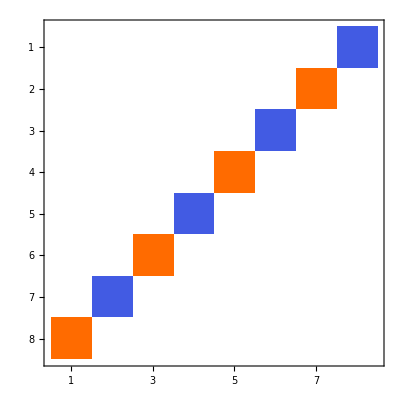
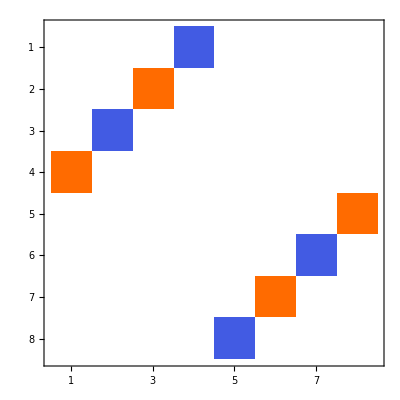
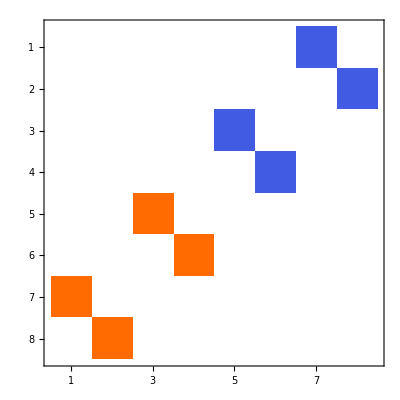
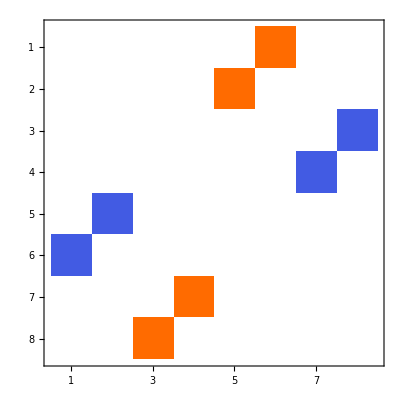
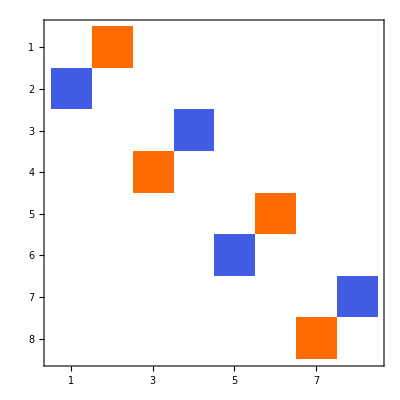
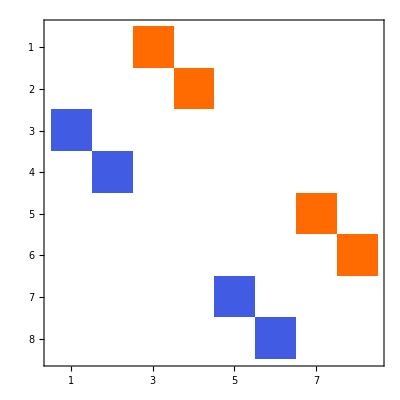

```mathematica
MatrixPlot/@vectors[testAlgebra,1]
```

where orange represents positive and blue negative numbers. Squares of the matrices gives minus unit matrix

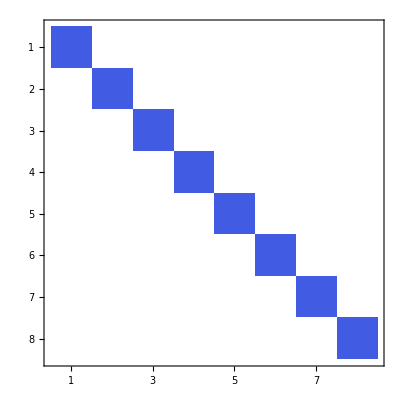
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

Test the interesting determinant property for vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  060

{(x[1]^2+x[2]^2+x[3]^2+x[4]^2+x[5]^2+x[6]^2)^4,(x[1]^2+x[2]^2+x[3]^2+x[4]^2+x[5]^2+x[6]^2)^4}

#### Cl[0,7], ->ℝ(8)⊕ℝ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[0,7];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Predefined color list of length 0 was exhausted. Start picking colors randomly.

100020200020

Base vector matrix representations. The  default setting,

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct","ElementaryRepresentations"->{Cl[2,0]->"IPauli[3,1]",Cl[1,0]->"Diagonal",Cl[0,2]->{"Q[1,2]"}},"QuaternionIsomorphismRules"->True},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[100020,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[100020200,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[100020200020,InvDeg[Lex],{1}]

Basis vectors are stored in   gaOrthonormalBasis[070,InvDeg[Lex],{1}]

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0)}

The ℝ(8)⊕ℝ(8) structure is more clearly seen from

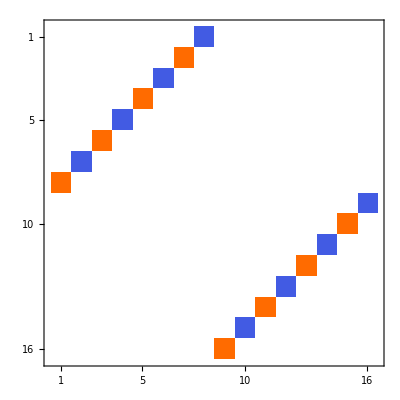
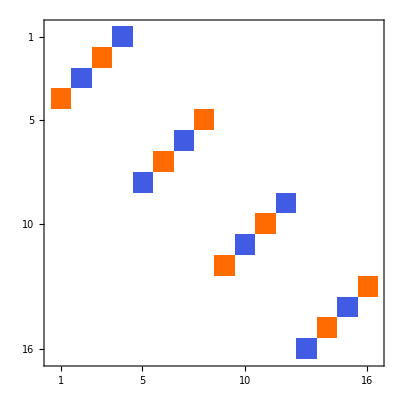
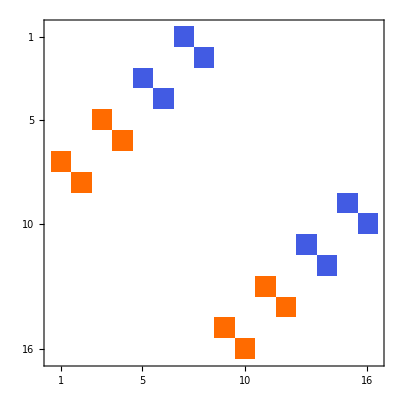
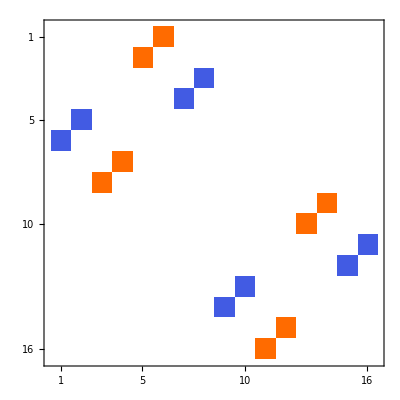
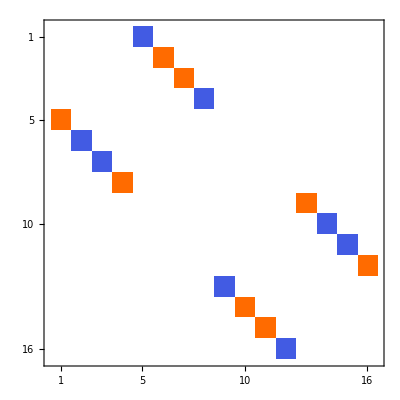
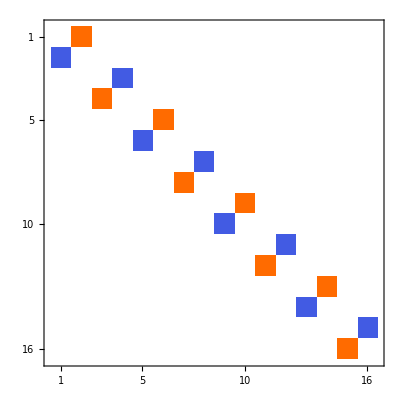
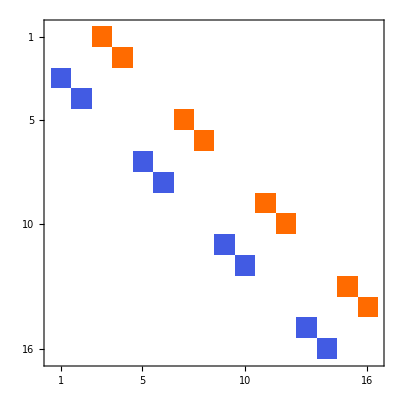

```mathematica
MatrixPlot/@vectors[testAlgebra,1]
```

These again squares to minus diagonal matrices

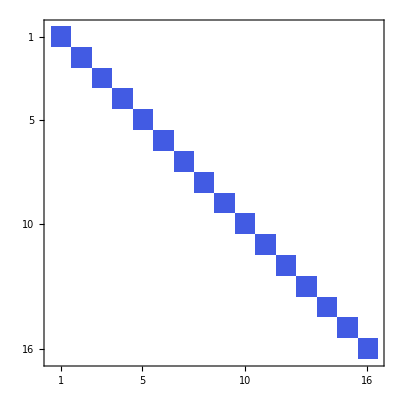
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

Test the interesting determinant property for vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  070

{(x[1]^2+x[2]^2+x[3]^2+x[4]^2+x[5]^2+x[6]^2+x[7]^2)^8,(x[1]^2+x[2]^2+x[3]^2+x[4]^2+x[5]^2+x[6]^2+x[7]^2)^8}

#### Cl[1,2], ->ℂ(2)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[1,2];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010110

Base vector matrix representations. The  default setting,

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct","ElementaryRepresentations"->{Cl[0,1]->"Complex",Cl[1,1]->"Antisymmetric"}},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[110,InvDeg[Lex],{1,2}]

Basis vectors are stored in   gaOrthonormalBasis[010110,InvDeg[Lex],{1}]

Basis vectors are stored in   gaOrthonormalBasis[120,InvDeg[Lex],{1}]

{(1 | 0
0 | -1),(0 | ⅈ
ⅈ | 0),(0 | 1
-1 | 0)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  120

{-x[1]^2+x[2]^2+x[3]^2,-x[1]^2+x[2]^2+x[3]^2}

#### Cl[1,3], ->ℍ(2)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[1,3];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

020110

Base vector matrix quaternionic representations.

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[020110,InvDeg[Lex],{1}]

Basis vectors are stored in   gaOrthonormalBasis[130,InvDeg[Lex],{1}]

{(1 | 0
0 | -1),(0 | 1020Quaternion
1020Quaternion | 0),(0 | 2020Quaternion
2020Quaternion | 0),(0 | 1
-1 | 0)}

Squares of quaternionic matrices can be calculated as

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0
0 | 1),(-1 | 0
0 | -1),(-1 | 0
0 | -1),(-1 | 0
0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  130

{-x[1]^2+x[2]^2+x[3]^2+x[4]^2,(x[1]^2-x[2]^2-x[3]^2-x[4]^2)^2}

Complex matrices can be calculated as

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct","ElementaryRepresentations"->{Cl[1,1]->"Antisymmetric",Cl[0,2]->"Pauli[1,2]"}},"Grades"->{1}])
```

{(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,2])
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,2],testAlgebra,False]
```

{(x[1]^2-x[2]^2-x[3]^2-x[4]^2)^2,(x[1]^2-x[2]^2-x[3]^2-x[4]^2)^2}

Or even symbolically as (one of many variants)

```mathematica
MatrixForm/@(vectors[testAlgebra,3]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct","ElementaryRepresentations"->{Cl[1,1]->"Trigonometric",Cl[0,2]->"HyperbolicTrigonometric"}},"Grades"->{1}])//Simplify
```

{(Sin[φ$23021] | Cos[φ$23021] | 0 | 0
Cos[φ$23021] | -Sin[φ$23021] | 0 | 0
0 | 0 | Sin[φ$23021] | Cos[φ$23021]
0 | 0 | Cos[φ$23021] | -Sin[φ$23021]),(0 | -ⅈ Sinh[φ$23012] | 0 | Cosh[φ$23012]
ⅈ Sinh[φ$23012] | 0 | -Cosh[φ$23012] | 0
0 | Cosh[φ$23012] | 0 | ⅈ Sinh[φ$23012]
-Cosh[φ$23012] | 0 | -ⅈ Sinh[φ$23012] | 0),(0 | Cosh[φ$23012] | 0 | ⅈ Sinh[φ$23012]
-Cosh[φ$23012] | 0 | -ⅈ Sinh[φ$23012] | 0
0 | ⅈ Sinh[φ$23012] | 0 | -Cosh[φ$23012]
-ⅈ Sinh[φ$23012] | 0 | Cosh[φ$23012] | 0),(-ⅈ Cos[φ$23021] | ⅈ Sin[φ$23021] | 0 | 0
ⅈ Sin[φ$23021] | ⅈ Cos[φ$23021] | 0 | 0
0 | 0 | -ⅈ Cos[φ$23021] | ⅈ Sin[φ$23021]
0 | 0 | ⅈ Sin[φ$23021] | ⅈ Cos[φ$23021])}

```mathematica
MatrixForm/@Simplify[(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,3])]
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,3],testAlgebra,False]//Simplify
```

{(-x[1]^2+x[2]^2+x[3]^2+x[4]^2)^2,(-x[1]^2+x[2]^2+x[3]^2+x[4]^2)^2}

#### Cl[1,4], ->ℍ(2)⊕ℍ(2)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[1,4];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

100020110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[100020,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[100020110,InvDeg[Lex],{1}]

Basis vectors are stored in   gaOrthonormalBasis[140,InvDeg[Lex],{1}]

{(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1020Quaternion | 0 | 0
1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 1020Quaternion
0 | 0 | 1020Quaternion | 0),(0 | 2020Quaternion | 0 | 0
2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 2020Quaternion
0 | 0 | 2020Quaternion | 0),(0 | 12020Quaternion | 0 | 0
12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | -12020Quaternion
0 | 0 | -12020Quaternion | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

Test the interesting determinant property for vectors representations. Interesting, that for quaternion matrices the polynomial degree doubles

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  140

{(x[1]^2-x[2]^2-x[3]^2-x[4]^2-x[5]^2)^2,(x[1]^2-x[2]^2-x[3]^2-x[4]^2-x[5]^2)^4}

Double check

```mathematica
MatrixForm/@vectors[testAlgebra,1]
```

{(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1020Quaternion | 0 | 0
1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 1020Quaternion
0 | 0 | 1020Quaternion | 0),(0 | 2020Quaternion | 0 | 0
2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 2020Quaternion
0 | 0 | 2020Quaternion | 0),(0 | 12020Quaternion | 0 | 0
12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | -12020Quaternion
0 | 0 | -12020Quaternion | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

```mathematica
gaDeterminantOfMV[Plus@@Table[vectors[testAlgebra,1][[i]]*x[i],{i,Length[vectors[testAlgebra,1]]}],Method->"Matrix"]//Factor
```

(x[1]^2-x[2]^2-x[3]^2-x[4]^2-x[5]^2)^4

```mathematica
gaDeterminantOfMV[Plus@@Table[vectors[testAlgebra,1][[i]]*x[i],{i,Length[vectors[testAlgebra,1]]}],Method->"FaddeevLieVerrierSouriau"]//Factor
```

(x[1]^2-x[2]^2-x[3]^2-x[4]^2-x[5]^2)^4

#### Cl[1,5], ->ℍ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[1,5];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

200020110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[200020,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[200020110,InvDeg[Lex],{1}]

Basis vectors are stored in   gaOrthonormalBasis[150,InvDeg[Lex],{1}]

{(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1020Quaternion | 0 | 0
1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 1020Quaternion
0 | 0 | 1020Quaternion | 0),(0 | 2020Quaternion | 0 | 0
2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 2020Quaternion
0 | 0 | 2020Quaternion | 0),(0 | 12020Quaternion | 0 | 0
12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | -12020Quaternion
0 | 0 | -12020Quaternion | 0),(0 | 0 | 0 | 12020Quaternion
0 | 0 | 12020Quaternion | 0
0 | 12020Quaternion | 0 | 0
12020Quaternion | 0 | 0 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

Squares of quaternionic matrices can be calculated as

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  150

{(x[1]^2-x[2]^2-x[3]^2-x[4]^2-x[5]^2-x[6]^2)^2,(x[1]^2-x[2]^2-x[3]^2-x[4]^2-x[5]^2-x[6]^2)^4}

#### Cl[1,6], ->ℂ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[1,6];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010200020110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[010200,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[010200020,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[010200020110,InvDeg[Lex],{1}]

Basis vectors are stored in   gaOrthonormalBasis[160,InvDeg[Lex],{1}]

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of  matrices can be calculated as

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  160

{(x[1]^2-x[2]^2-x[3]^2-x[4]^2-x[5]^2-x[6]^2-x[7]^2)^4,(x[1]^2-x[2]^2-x[3]^2-x[4]^2-x[5]^2-x[6]^2-x[7]^2)^4}

#### Cl[1,7], ->ℝ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[1,7];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

020200020110

Base vector matrix representations using default settings

Basis vectors are stored in   gaOrthonormalBasis[020200,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[020200020,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[170,InvDeg[Lex],{1}]

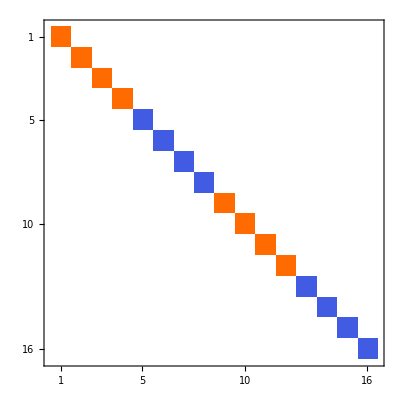
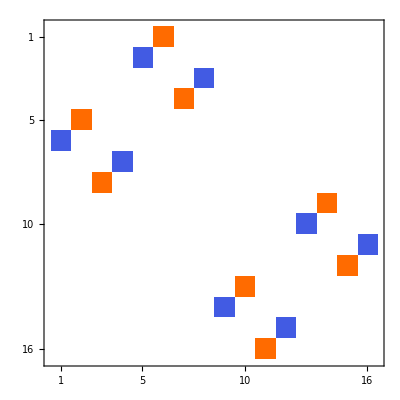
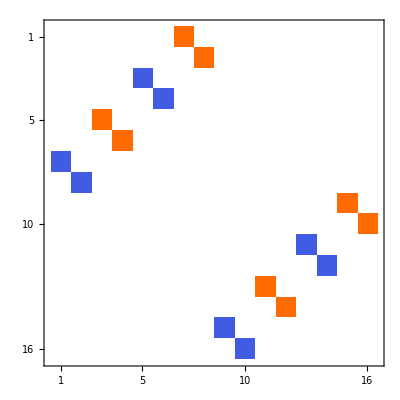
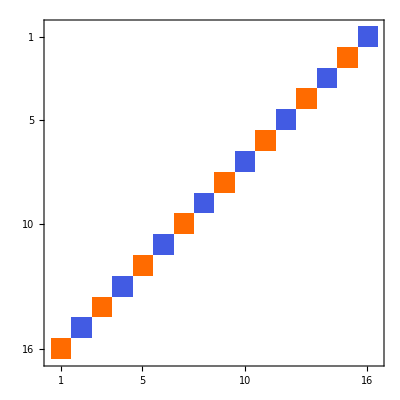
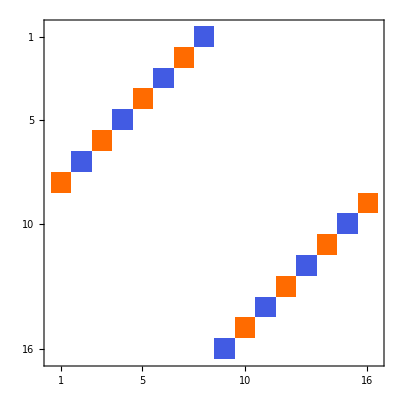
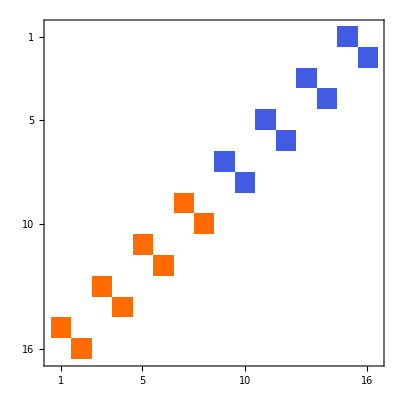
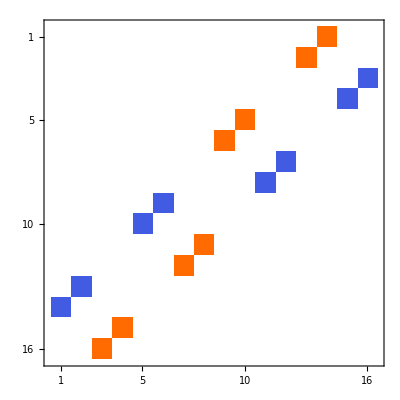
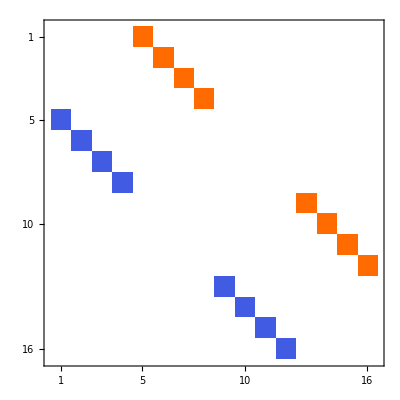

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct","QuaternionIsomorphismRules"->True},"Grades"->{1}])
```

We can make them sparse with

```mathematica
vectors[testAlgebra,2]=SparseArray/@vectors[testAlgebra,1]
```

{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

Squares of sparse matrices can be calculated using Dot[ ]. Unfortunately gaGeometricMatrixProduct[ ] would expand them to dense matrix and it will take much more time to multiply

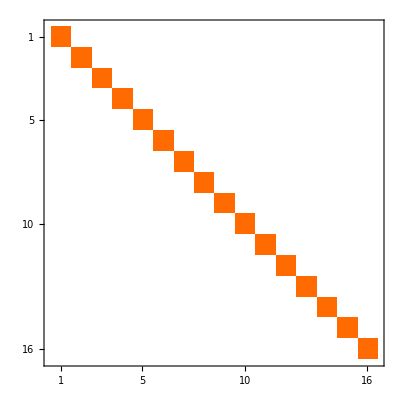
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot/@(Dot[#,#]&/@vectors[testAlgebra,2])
```

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  170

{(x[1]^2-x[2]^2-x[3]^2-x[4]^2-x[5]^2-x[6]^2-x[7]^2-x[8]^2)^8,(x[1]^2-x[2]^2-x[3]^2-x[4]^2-x[5]^2-x[6]^2-x[7]^2-x[8]^2)^8}

#### Cl[2,1], ->ℝ(2)⊕ℝ(2)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[2,1];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

100110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct","QuaternionIsomorphismRules"->True},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[100110,InvDeg[Lex],{1}]

gaDefineMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct","BaseVectorAlgebra"→1,"TargetMatrices"→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

Basis vectors are stored in   gaOrthonormalBasis[210,InvDeg[Lex],{1}]

{(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

There exist, however 2×2 dimensional real representation!  These representations are not universal (see Jayme Vaz, Jr.; Roldao Da Rocha, Jr. “An Introduction to Clifford Algebras and Spinors”, 2016,Oxford.

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,2]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct","ElementaryRepresentations"->{Cl[0,1]->"Complex",Cl[1,1]->"Antisymmetric"},"QuaternionIsomorphismRules"->True,"BaseVectorAlgebra"->Cl[1,2],"TargetMatrices"->Reals},"Grades"->{1}]),{All,2}]
```

{{{0,-1},(-1
0)},{{1,0},(0
-1)},{{0,1},(-1
0)}}

Squares of sparse matrices can be calculated using Dot[ ]. Unfortunately gaGeometricMatrixProduct[ ] would expand them to dense matrix and it will take much more time to multiply

```mathematica
MatrixForm/@(Dot[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

```mathematica
MapAt[MatrixForm,MapAt[Dot[#,#]&,vectors[testAlgebra,2],{All,2}],{All,2}]
```

{{{0,-1},1},{{1,0},1},{{0,1},1}}

Test the interesting determinant property for both vectors representations (note the difference in powers)

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  210

{(x[1]^2+x[2]^2-x[3]^2)^2,(x[1]^2+x[2]^2-x[3]^2)^2}

```mathematica
vectors[testAlgebra,2]
```

{{{0,-1},{-1,0}},{{1,0},{0,-1}},{{0,1},{-1,0}}}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,2],testAlgebra,False]
```

{-x[1]^2-x[2]^2+x[3]^2,-x[1]^2-x[2]^2+x[3]^2}

#### Cl[2,2], ->ℝ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[2,2];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[110110,InvDeg[Lex],{1}]

Basis vectors are stored in   gaOrthonormalBasis[220,InvDeg[Lex],{1}]

{(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using Dot[ ]. Unfortunately gaGeometricMatrixProduct[ ] would expand them to dense matrix and it will take much more time to multiply

```mathematica
MatrixForm/@(Dot[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

Test the interesting determinant property for vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  220

{(x[1]^2+x[2]^2-x[3]^2-x[4]^2)^2,(x[1]^2+x[2]^2-x[3]^2-x[4]^2)^2}

#### Cl[2,3], ->ℂ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[2,3];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[010110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[010110110,InvDeg[Lex],{1}]

Basis vectors are stored in   gaOrthonormalBasis[230,InvDeg[Lex],{1}]

{(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using Dot[ ]. Unfortunately gaGeometricMatrixProduct[ ] would expand them to dense matrix and it will take much more time to multiply

```mathematica
MatrixForm/@(Dot[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

Test the interesting determinant property for vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  230

{(x[1]^2+x[2]^2-x[3]^2-x[4]^2-x[5]^2)^2,(x[1]^2+x[2]^2-x[3]^2-x[4]^2-x[5]^2)^2}

#### Cl[2,4], ->ℍ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[2,4];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

020110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[020110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[020110110,InvDeg[Lex],{1}]

Basis vectors are stored in   gaOrthonormalBasis[240,InvDeg[Lex],{1}]

{(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | 1020Quaternion
0 | 0 | 1020Quaternion | 0
0 | 1020Quaternion | 0 | 0
1020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 2020Quaternion
0 | 0 | 2020Quaternion | 0
0 | 2020Quaternion | 0 | 0
2020Quaternion | 0 | 0 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  240

{(x[1]^2+x[2]^2-x[3]^2-x[4]^2-x[5]^2-x[6]^2)^2,(x[1]^2+x[2]^2-x[3]^2-x[4]^2-x[5]^2-x[6]^2)^4}

#### Cl[2,5], ->ℍ(4)⊕ℍ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[2,5];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

100020110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[100020,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[100020110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[100020110110,InvDeg[Lex],{1}]

Basis vectors are stored in   gaOrthonormalBasis[250,InvDeg[Lex],{1}]

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

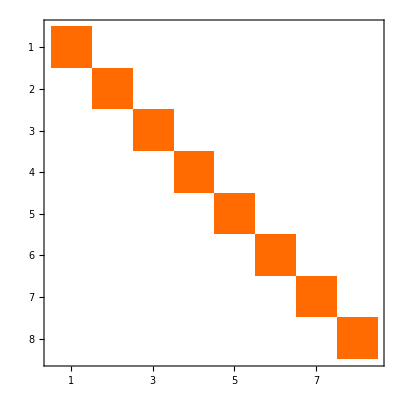
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x[1]^2+x[2]^2-x[3]^2-x[4]^2-x[5]^2-x[6]^2-x[7]^2)^4,(x[1]^2+x[2]^2-x[3]^2-x[4]^2-x[5]^2-x[6]^2-x[7]^2)^8}

#### Cl[2,6], ->ℍ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[2,6];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

200020110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[200020,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[200020110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[260,InvDeg[Lex],{1}]

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  260

{(x[1]^2+x[2]^2-x[3]^2-x[4]^2-x[5]^2-x[6]^2-x[7]^2-x[8]^2)^4,(x[1]^2+x[2]^2-x[3]^2-x[4]^2-x[5]^2-x[6]^2-x[7]^2-x[8]^2)^8}

#### Cl[2,7], ->ℂ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[2,7];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010200020110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[010200,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[010200020,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[010200020110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[270,InvDeg[Lex],{1}]

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  270

{(x[1]^2+x[2]^2-x[3]^2-x[4]^2-x[5]^2-x[6]^2-x[7]^2-x[8]^2-x[9]^2)^8,(x[1]^2+x[2]^2-x[3]^2-x[4]^2-x[5]^2-x[6]^2-x[7]^2-x[8]^2-x[9]^2)^8}

#### Cl[3,0], ->ℂ(2)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[3,0];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010200

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1},"BasisVectorsReordering"->{2,3,1}])
```

Basis vectors are stored in   gaOrthonormalBasis[300,InvDeg[Lex],{1}]

{(1 | 0
0 | -1),(0 | 1
1 | 0),(0 | ⅈ
-ⅈ | 0)}

Base vector matrix representations using symbolic matrix. Possible  types are "Trigonometric"
"TrigonometricAntisymmetric"
"HyperbolicTrigonometric"
"HyperbolicTrigonometricAntisymmetric"

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct","ElementaryRepresentations"->{010->"Complex",200->"Trigonometric"}},"Grades"->{1}])
```

{(0 | ⅈ (Cos[φ$61495]^2+Sin[φ$61495]^2)
ⅈ (-Cos[φ$61495]^2-Sin[φ$61495]^2) | 0),(Sin[φ$61495] | Cos[φ$61495]
Cos[φ$61495] | -Sin[φ$61495]),(-Cos[φ$61495] | Sin[φ$61495]
Sin[φ$61495] | Cos[φ$61495])}

```mathematica
MatrixForm/@(vectors[testAlgebra,2]//Simplify)
```

{(0 | ⅈ
-ⅈ | 0),(Sin[φ$61495] | Cos[φ$61495]
Cos[φ$61495] | -Sin[φ$61495]),(-Cos[φ$61495] | Sin[φ$61495]
Sin[φ$61495] | Cos[φ$61495])}

The other form is

```mathematica
MatrixForm/@(vectors[testAlgebra,3]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct","ElementaryRepresentations"->{010->"Complex",200->"HyperbolicTrigonometric"}},"Grades"->{1}])
```

{(0 | ⅈ (-Cosh[φ$61562]^2+Sinh[φ$61562]^2)
ⅈ (Cosh[φ$61562]^2-Sinh[φ$61562]^2) | 0),(-ⅈ Sinh[φ$61562] | Cosh[φ$61562]
Cosh[φ$61562] | ⅈ Sinh[φ$61562]),(Cosh[φ$61562] | ⅈ Sinh[φ$61562]
ⅈ Sinh[φ$61562] | -Cosh[φ$61562])}

```mathematica
MatrixForm/@(vectors[testAlgebra,3]//Simplify)
```

{(0 | -ⅈ
ⅈ | 0),(-ⅈ Sinh[φ$61562] | Cosh[φ$61562]
Cosh[φ$61562] | ⅈ Sinh[φ$61562]),(Cosh[φ$61562] | ⅈ Sinh[φ$61562]
ⅈ Sinh[φ$61562] | -Cosh[φ$61562])}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0
0 | 1),(1 | 0
0 | 1),(1 | 0
0 | 1)}

```mathematica
MatrixForm/@(Simplify[gaGeometricMatrixProduct[#,#]]&/@vectors[testAlgebra,2])
```

{(1 | 0
0 | 1),(1 | 0
0 | 1),(1 | 0
0 | 1)}

```mathematica
MatrixForm/@(Simplify[gaGeometricMatrixProduct[#,#]]&/@vectors[testAlgebra,3])
```

{(1 | 0
0 | 1),(1 | 0
0 | 1),(1 | 0
0 | 1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  300

{-x[1]^2-x[2]^2-x[3]^2,-x[1]^2-x[2]^2-x[3]^2}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,2],testAlgebra,False]//Simplify
```

{-x[1]^2-x[2]^2-x[3]^2,-x[1]^2-x[2]^2-x[3]^2}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,3],testAlgebra,False]//Simplify
```

{-x[1]^2-x[2]^2-x[3]^2,-x[1]^2-x[2]^2-x[3]^2}

Matrix determinant computation for complex algebras

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

{(0 | ⅈ
-ⅈ | 0),(1 | 0
0 | -1),(0 | 1
1 | 0)}

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=ArrayFlatten[#,2]&/@(vectors[testAlgebra,1]/.{0->{{0,0},{0,0}},1->{{1,0},{0,1}},-1->{{-1,0},{0,-1}},-I->{{0,-1},{1,0}},I->{{0,1},{-1,0}}}))
```

{(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)}

```mathematica
gaDefineOrthonormalBasis[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  300

{1,1300,2300,3300,12300,13300,23300,123300}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[Table[𝕖[i]->vectors[testAlgebra,2][[i]],{i,3}]],{All,2}]
```

{1300→(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),2300→(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),3300→(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),12300→(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),13300→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),23300→(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),123300→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0)}

```mathematica
Det[gaToMatrixRepresentation[gaGeneralMultivector[a,testAlgebra],testAlgebra]]
gaDeterminantOfMV[gaGeneralMultivector[a,testAlgebra]]-%//Expand
```

gaToMatrixRepresentation::NotBottDimension: You are using matrix representation of algebra 3 that do not match dimensions 2, listed in Bott periodicity table. Conversion to/from matrix representation may need adjusting the option "gaFieldFactor" value. These representations are inapropriate for non-diagonalizable MVs

a[0]^4-2 a[0]^2 a[1]^2+a[1]^4-2 a[0]^2 a[2]^2+2 a[1]^2 a[2]^2+a[2]^4-2 a[0]^2 a[3]^2+2 a[1]^2 a[3]^2+2 a[2]^2 a[3]^2+a[3]^4+2 a[0]^2 a[4]^2-2 a[1]^2 a[4]^2-2 a[2]^2 a[4]^2+2 a[3]^2 a[4]^2+a[4]^4-8 a[2] a[3] a[4] a[5]+2 a[0]^2 a[5]^2-2 a[1]^2 a[5]^2+2 a[2]^2 a[5]^2-2 a[3]^2 a[5]^2+2 a[4]^2 a[5]^2+a[5]^4+8 a[1] a[3] a[4] a[6]-8 a[1] a[2] a[5] a[6]+2 a[0]^2 a[6]^2+2 a[1]^2 a[6]^2-2 a[2]^2 a[6]^2-2 a[3]^2 a[6]^2+2 a[4]^2 a[6]^2+2 a[5]^2 a[6]^2+a[6]^4-8 a[0] a[3] a[4] a[7]+8 a[0] a[2] a[5] a[7]-8 a[0] a[1] a[6] a[7]+2 a[0]^2 a[7]^2+2 a[1]^2 a[7]^2+2 a[2]^2 a[7]^2+2 a[3]^2 a[7]^2-2 a[4]^2 a[7]^2-2 a[5]^2 a[7]^2-2 a[6]^2 a[7]^2+a[7]^4

0

#### Cl[3,1], ->ℝ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[3,1];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

200110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[200110,InvDeg[Lex],{1}]

Basis vectors are stored in   gaOrthonormalBasis[310,InvDeg[Lex],{1}]

{(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  310

{(x[1]^2+x[2]^2+x[3]^2-x[4]^2)^2,(x[1]^2+x[2]^2+x[3]^2-x[4]^2)^2}

#### Cl[3,2], ->ℝ(4)⊕ℝ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[3,2];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

100110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[100110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[100110110,InvDeg[Lex],{1}]

gaDefineMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct","BaseVectorAlgebra"→2,"TargetMatrices"→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

Basis vectors are stored in   gaOrthonormalBasis[320,InvDeg[Lex],{1}]

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  320

{(x[1]^2+x[2]^2+x[3]^2-x[4]^2-x[5]^2)^4,(x[1]^2+x[2]^2+x[3]^2-x[4]^2-x[5]^2)^4}

#### Cl[3,3], ->ℝ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[3,3];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[110110110,InvDeg[Lex],{1}]

Basis vectors are stored in   gaOrthonormalBasis[330,InvDeg[Lex],{1}]

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  330

{(x[1]^2+x[2]^2+x[3]^2-x[4]^2-x[5]^2-x[6]^2)^4,(x[1]^2+x[2]^2+x[3]^2-x[4]^2-x[5]^2-x[6]^2)^4}

#### Cl[3,4], ->ℂ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[3,4];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[010110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[010110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[010110110110,InvDeg[Lex],{1}]

Basis vectors are stored in   gaOrthonormalBasis[340,InvDeg[Lex],{1}]

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  340

{(x[1]^2+x[2]^2+x[3]^2-x[4]^2-x[5]^2-x[6]^2-x[7]^2)^4,(x[1]^2+x[2]^2+x[3]^2-x[4]^2-x[5]^2-x[6]^2-x[7]^2)^4}

#### Cl[3,5], ->ℍ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[3,5];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

020110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[020110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[020110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[350,InvDeg[Lex],{1}]

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations.

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  350

{(x[1]^2+x[2]^2+x[3]^2-x[4]^2-x[5]^2-x[6]^2-x[7]^2-x[8]^2)^4,(x[1]^2+x[2]^2+x[3]^2-x[4]^2-x[5]^2-x[6]^2-x[7]^2-x[8]^2)^8}

#### Cl[3,6], ->ℍ(8)⊕ℍ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[3,6];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

100020110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[100020,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[100020110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[100020110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[360,InvDeg[Lex],{1}]

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  360

{(x[1]^2+x[2]^2+x[3]^2-x[4]^2-x[5]^2-x[6]^2-x[7]^2-x[8]^2-x[9]^2)^8,(x[1]^2+x[2]^2+x[3]^2-x[4]^2-x[5]^2-x[6]^2-x[7]^2-x[8]^2-x[9]^2)^16}

#### Cl[3,7], ->ℍ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[3,7];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

200020110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[200020,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[200020110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[370,InvDeg[Lex],{1}]

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representation. Now result is too large to factor, so calculate just difference

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]//Factor
```

Running algebra is: gaRunningAlgebra=  370

{(x[1]^2+x[2]^2+x[3]^2-x[4]^2-x[5]^2-x[6]^2-x[7]^2-x[8]^2-x[9]^2-x[10]^2)^8,(x[1]^2+x[2]^2+x[3]^2-x[4]^2-x[5]^2-x[6]^2-x[7]^2-x[8]^2-x[9]^2-x[10]^2)^16}

#### Cl[4,0], ->ℍ(2)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[4,0];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

020200

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[020200,InvDeg[Lex],{1}]

Basis vectors are stored in   gaOrthonormalBasis[400,InvDeg[Lex],{1}]

{(0 | 1020Quaternion
-1020Quaternion | 0),(0 | 2020Quaternion
-2020Quaternion | 0),(1 | 0
0 | -1),(0 | 1
1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0
0 | 1),(1 | 0
0 | 1),(1 | 0
0 | 1),(1 | 0
0 | 1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  400

{-x[1]^2-x[2]^2-x[3]^2-x[4]^2,(x[1]^2+x[2]^2+x[3]^2+x[4]^2)^2}

#### Cl[4,1], ->ℂ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[4,1];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010200110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[010200,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[010200110,InvDeg[Lex],{1}]

Basis vectors are stored in   gaOrthonormalBasis[410,InvDeg[Lex],{1}]

{(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  410

{(x[1]^2+x[2]^2+x[3]^2+x[4]^2-x[5]^2)^2,(x[1]^2+x[2]^2+x[3]^2+x[4]^2-x[5]^2)^2}

#### Cl[4,2], ->ℝ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[4,2];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

200110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[200110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[200110110,InvDeg[Lex],{1}]

Basis vectors are stored in   gaOrthonormalBasis[420,InvDeg[Lex],{1}]

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  420

{(x[1]^2+x[2]^2+x[3]^2+x[4]^2-x[5]^2-x[6]^2)^4,(x[1]^2+x[2]^2+x[3]^2+x[4]^2-x[5]^2-x[6]^2)^4}

#### Cl[4,3], ->ℝ(8)⊕ℝ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[4,3];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

100110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[100110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[100110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[100110110110,InvDeg[Lex],{1}]

gaDefineMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct","BaseVectorAlgebra"→3,"TargetMatrices"→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

Basis vectors are stored in   gaOrthonormalBasis[430,InvDeg[Lex],{1}]

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  430

{(x[1]^2+x[2]^2+x[3]^2+x[4]^2-x[5]^2-x[6]^2-x[7]^2)^8,(x[1]^2+x[2]^2+x[3]^2+x[4]^2-x[5]^2-x[6]^2-x[7]^2)^8}

#### Cl[4,4], ->ℝ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[4,4];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

110110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[110110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[440,InvDeg[Lex],{1}]

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  440

{(x[1]^2+x[2]^2+x[3]^2+x[4]^2-x[5]^2-x[6]^2-x[7]^2-x[8]^2)^8,(x[1]^2+x[2]^2+x[3]^2+x[4]^2-x[5]^2-x[6]^2-x[7]^2-x[8]^2)^8}

#### Cl[4,5], ->ℂ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[4,5];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010110110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[010110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[010110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[010110110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[450,InvDeg[Lex],{1}]

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  450

{(x[1]^2+x[2]^2+x[3]^2+x[4]^2-x[5]^2-x[6]^2-x[7]^2-x[8]^2-x[9]^2)^8,(x[1]^2+x[2]^2+x[3]^2+x[4]^2-x[5]^2-x[6]^2-x[7]^2-x[8]^2-x[9]^2)^8}

#### Cl[4,6], ->ℍ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[4,6];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

020110110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[020110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[020110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[460,InvDeg[Lex],{1}]

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

#### Cl[4,7], ->ℍ(16)⊕ℍ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[4,7];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

100020110110110110

Base vector matrix representations using default settings

Basis vectors are stored in   gaOrthonormalBasis[100020,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[100020110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[100020110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[470,InvDeg[Lex],{1}]

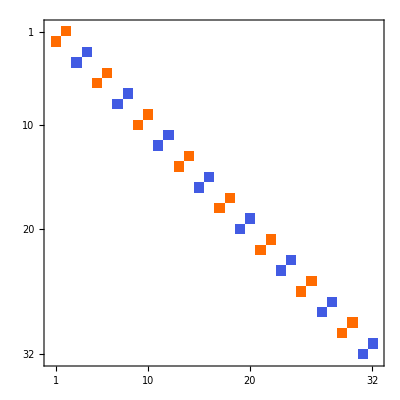
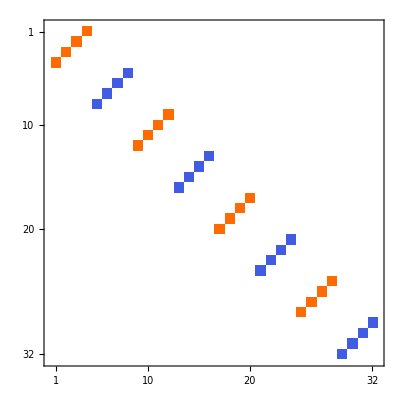
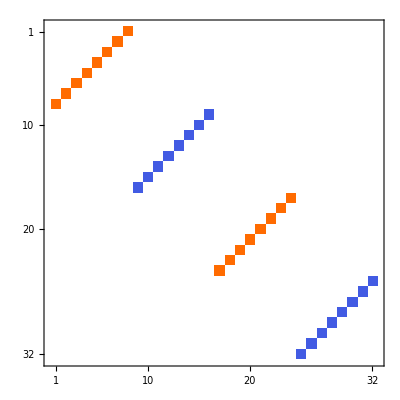
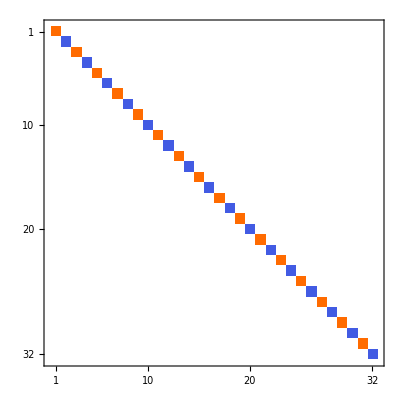
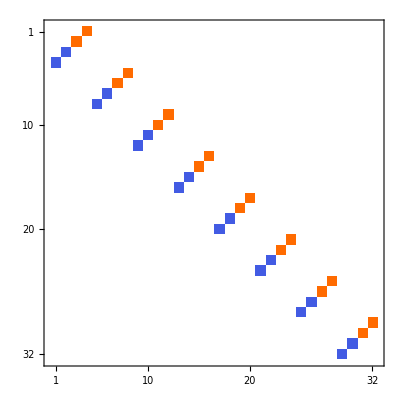
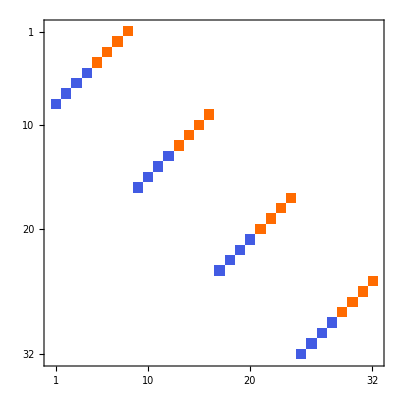
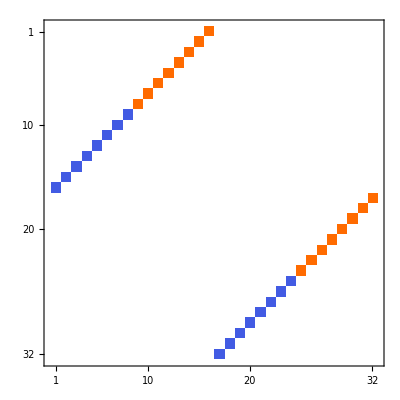
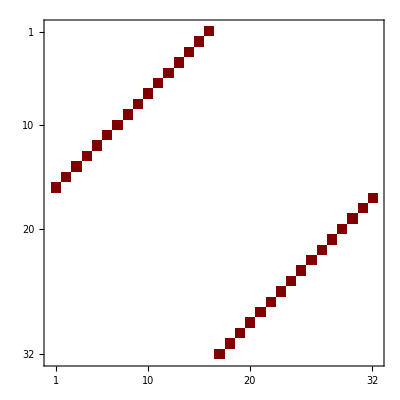
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

It is easy to see that dark red entries correspond to quaternions (i.𝕖. symbolic entries)

```mathematica
vectors[testAlgebra,1][[8]]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

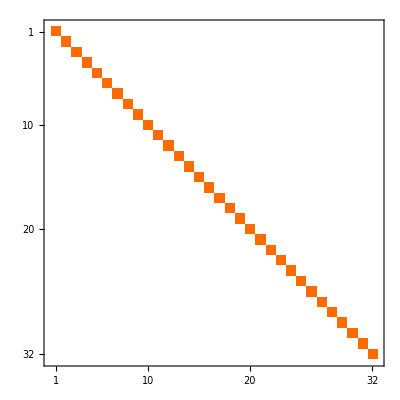
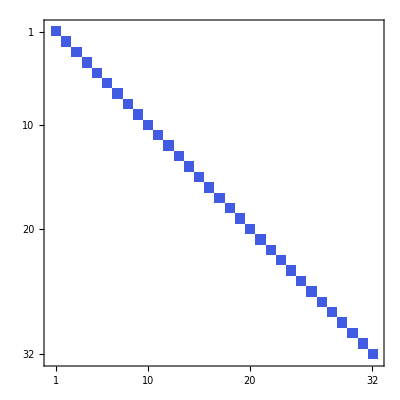
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

#### Cl[5,0], ->ℍ(2)⊕ℍ(2)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[5,0];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

100020200

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[100020,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[100020200,InvDeg[Lex],{1}]

Basis vectors are stored in   gaOrthonormalBasis[500,InvDeg[Lex],{1}]

{(0 | 1020Quaternion | 0 | 0
-1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 1020Quaternion
0 | 0 | -1020Quaternion | 0),(0 | 2020Quaternion | 0 | 0
-2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 2020Quaternion
0 | 0 | -2020Quaternion | 0),(0 | 12020Quaternion | 0 | 0
-12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | -12020Quaternion
0 | 0 | 12020Quaternion | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

Test the interesting determinant property for vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  500

{(x[1]^2+x[2]^2+x[3]^2+x[4]^2+x[5]^2)^2,(x[1]^2+x[2]^2+x[3]^2+x[4]^2+x[5]^2)^4}

#### Cl[5,1], ->ℍ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[5,1];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

020200110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[020200,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[020200110,InvDeg[Lex],{1}]

Basis vectors are stored in   gaOrthonormalBasis[510,InvDeg[Lex],{1}]

{(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | 1020Quaternion
0 | 0 | 1020Quaternion | 0
0 | -1020Quaternion | 0 | 0
-1020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 2020Quaternion
0 | 0 | 2020Quaternion | 0
0 | -2020Quaternion | 0 | 0
-2020Quaternion | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

Test the interesting determinant property for  vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  510

{(x[1]^2+x[2]^2+x[3]^2+x[4]^2+x[5]^2-x[6]^2)^2,(x[1]^2+x[2]^2+x[3]^2+x[4]^2+x[5]^2-x[6]^2)^4}

#### Cl[5,2], ->ℂ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[5,2];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010200110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[010200,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[010200110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[010200110110,InvDeg[Lex],{1}]

Basis vectors are stored in   gaOrthonormalBasis[520,InvDeg[Lex],{1}]

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinant property for vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  520

{(x[1]^2+x[2]^2+x[3]^2+x[4]^2+x[5]^2-x[6]^2-x[7]^2)^4,(x[1]^2+x[2]^2+x[3]^2+x[4]^2+x[5]^2-x[6]^2-x[7]^2)^4}

#### Cl[5,3], ->ℝ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[5,3];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

200110110110

Base vector matrix representations using default settings

Basis vectors are stored in   gaOrthonormalBasis[200110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[200110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[530,InvDeg[Lex],{1}]

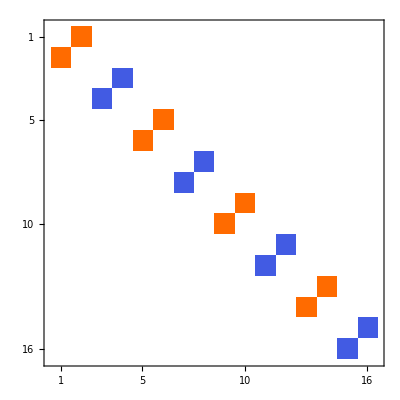
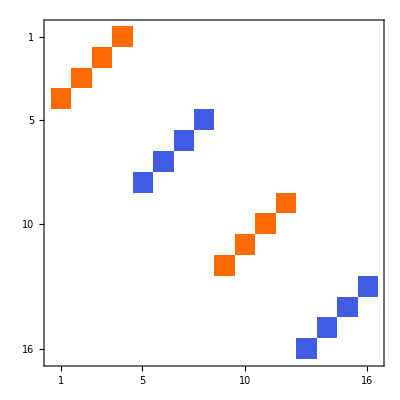
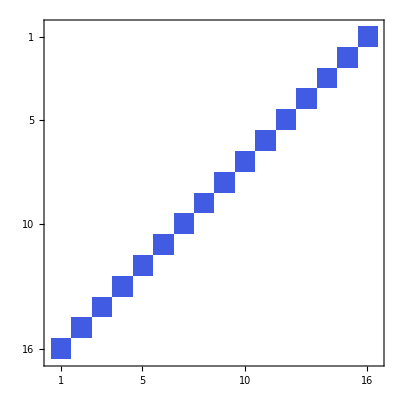
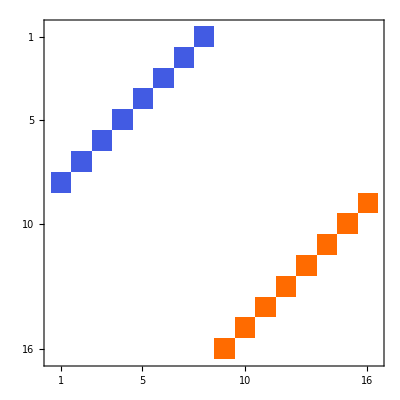
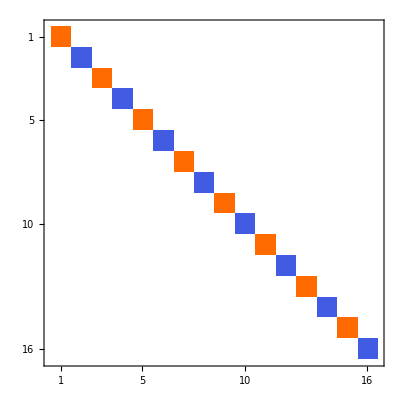
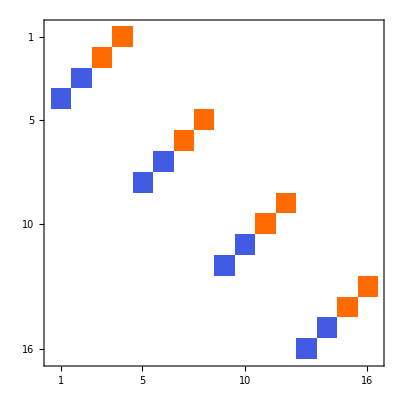
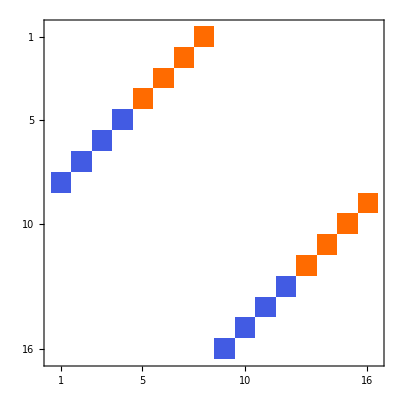
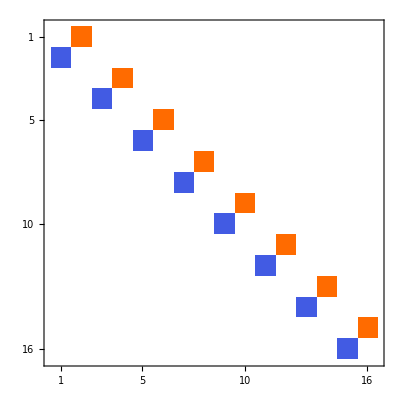

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property for vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  530

{(x[1]^2+x[2]^2+x[3]^2+x[4]^2+x[5]^2-x[6]^2-x[7]^2-x[8]^2)^8,(x[1]^2+x[2]^2+x[3]^2+x[4]^2+x[5]^2-x[6]^2-x[7]^2-x[8]^2)^8}

#### Cl[5,4], ->ℝ(16)⊕ℝ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[5,4];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

100110110110110

Base vector matrix representations using default settings

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[100110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[100110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[100110110110,InvDeg[Lex],{0,1}]

gaDefineMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct","BaseVectorAlgebra"→4,"TargetMatrices"→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

Basis vectors are stored in   gaOrthonormalBasis[540,InvDeg[Lex],{1}]

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property for vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  540

{(x[1]^2+x[2]^2+x[3]^2+x[4]^2+x[5]^2-x[6]^2-x[7]^2-x[8]^2-x[9]^2)^16,(x[1]^2+x[2]^2+x[3]^2+x[4]^2+x[5]^2-x[6]^2-x[7]^2-x[8]^2-x[9]^2)^16}

#### Cl[5,5], ->ℝ(32)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[5,5];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

110110110110110

Base vector matrix representations using default settings

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[110110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[550,InvDeg[Lex],{1}]

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  Dot[ ].

```mathematica
MatrixPlot/@(Dot[#,#]&/@(SparseArray/@vectors[testAlgebra,1]))
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  550

{(x[1]^2+x[2]^2+x[3]^2+x[4]^2+x[5]^2-x[6]^2-x[7]^2-x[8]^2-x[9]^2-x[10]^2)^16,(x[1]^2+x[2]^2+x[3]^2+x[4]^2+x[5]^2-x[6]^2-x[7]^2-x[8]^2-x[9]^2-x[10]^2)^16}

#### Cl[5,6], ->ℂ(32)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[5,6];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010110110110110110

Base vector matrix representations using default settings

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[010110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[010110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[010110110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[560,InvDeg[Lex],{1}]

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property. Calculation of matrix determinant  now takes too much memory, calculate only Clifford result

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

Running algebra is: gaRunningAlgebra=  560

(-x[1]^2-x[2]^2-x[3]^2-x[4]^2-x[5]^2+x[6]^2+x[7]^2+x[8]^2+x[9]^2+x[10]^2+x[11]^2)^16

#### Cl[5,7], ->ℍ(32)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[5,7];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

020110110110110110

Base vector matrix representations using default settings

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[020110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[020110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[570,InvDeg[Lex],{1}]

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

Running algebra is: gaRunningAlgebra=  570

(-x[1]^2-x[2]^2-x[3]^2-x[4]^2-x[5]^2+x[6]^2+x[7]^2+x[8]^2+x[9]^2+x[10]^2+x[11]^2+x[12]^2)^16

#### Cl[6,0], ->ℍ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[6,0];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

200020200

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[200020,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[200020200,InvDeg[Lex],{1}]

Basis vectors are stored in   gaOrthonormalBasis[600,InvDeg[Lex],{1}]

{(0 | 1020Quaternion | 0 | 0
-1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 1020Quaternion
0 | 0 | -1020Quaternion | 0),(0 | 2020Quaternion | 0 | 0
-2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 2020Quaternion
0 | 0 | -2020Quaternion | 0),(0 | 12020Quaternion | 0 | 0
-12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | -12020Quaternion
0 | 0 | 12020Quaternion | 0),(0 | 0 | 0 | 12020Quaternion
0 | 0 | -12020Quaternion | 0
0 | 12020Quaternion | 0 | 0
-12020Quaternion | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  600

{(x[1]^2+x[2]^2+x[3]^2+x[4]^2+x[5]^2+x[6]^2)^2,(x[1]^2+x[2]^2+x[3]^2+x[4]^2+x[5]^2+x[6]^2)^4}

#### Cl[6,1], ->ℍ(4)⊕ℍ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[6,1];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

100020200110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[100020,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[100020200,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[100020200110,InvDeg[Lex],{1}]

Basis vectors are stored in   gaOrthonormalBasis[610,InvDeg[Lex],{1}]

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | -1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
-1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | -1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | -1020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | -2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
-2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | -2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | -2020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
-12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  610

{(x[1]^2+x[2]^2+x[3]^2+x[4]^2+x[5]^2+x[6]^2-x[7]^2)^4,(x[1]^2+x[2]^2+x[3]^2+x[4]^2+x[5]^2+x[6]^2-x[7]^2)^8}

#### Cl[6,2], ->ℍ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[6,2];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

020200110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[020200,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[020200110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[620,InvDeg[Lex],{1}]

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | -1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | -1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | -1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
-1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | -2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | -2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | -2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
-2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  620

{(x[1]^2+x[2]^2+x[3]^2+x[4]^2+x[5]^2+x[6]^2-x[7]^2-x[8]^2)^4,(x[1]^2+x[2]^2+x[3]^2+x[4]^2+x[5]^2+x[6]^2-x[7]^2-x[8]^2)^8}

#### Cl[6,3], ->ℂ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[6,3];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010200110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[010200,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[010200110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[010200110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[630,InvDeg[Lex],{1}]

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  630

{(x[1]^2+x[2]^2+x[3]^2+x[4]^2+x[5]^2+x[6]^2-x[7]^2-x[8]^2-x[9]^2)^8,(x[1]^2+x[2]^2+x[3]^2+x[4]^2+x[5]^2+x[6]^2-x[7]^2-x[8]^2-x[9]^2)^8}

#### Cl[6,4], ->ℝ(32)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[6,4];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

200110110110110

Base vector matrix representations using default settings

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[200110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[200110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[640,InvDeg[Lex],{1}]

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property. Calculation of matrix determinant  now takes too much memory, calculate only Clifford result

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

Running algebra is: gaRunningAlgebra=  640

(-x[1]^2-x[2]^2-x[3]^2-x[4]^2-x[5]^2-x[6]^2+x[7]^2+x[8]^2+x[9]^2+x[10]^2)^16

#### Cl[6,5], ->ℝ(32)⊕ℝ(32)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[6,5];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

100110110110110110

Base vector matrix representations using default settings. Due to large matrix size we just plot matrix shapes (orange points are +1, blue represents -1)

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[100110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[100110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[100110110110,InvDeg[Lex],{0,1}]

gaDefineMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct","BaseVectorAlgebra"→5,"TargetMatrices"→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

Basis vectors are stored in   gaOrthonormalBasis[650,InvDeg[Lex],{1}]

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property. Calculation of matrix determinant  now takes too much memory, calculate only Clifford result

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

Running algebra is: gaRunningAlgebra=  650

(-x[1]^2-x[2]^2-x[3]^2-x[4]^2-x[5]^2-x[6]^2+x[7]^2+x[8]^2+x[9]^2+x[10]^2+x[11]^2)^32

#### Cl[6,6], ->ℝ(64)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[6,6];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

110110110110110110

Base vector matrix representations using default settings. Due to large matrix size we just plot matrix shapes (orange points are +1, blue represents -1)

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[110110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[660,InvDeg[Lex],{1}]

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property. Calculation of matrix determinant  now takes too much memory, calculate only Clifford result

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

Running algebra is: gaRunningAlgebra=  660

(-x[1]^2-x[2]^2-x[3]^2-x[4]^2-x[5]^2-x[6]^2+x[7]^2+x[8]^2+x[9]^2+x[10]^2+x[11]^2+x[12]^2)^32

#### Cl[6,7], ->ℂ(64)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[6,7];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010110110110110110110

Base vector matrix representations using default settings. Due to large matrix size we just plot matrix shapes (orange points are +1, blue represents -1)

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[010110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[010110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[010110110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[670,InvDeg[Lex],{1}]

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property. Calculation of matrix determinant  now takes too much memory, calculate only Clifford result

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

Running algebra is: gaRunningAlgebra=  670

(-x[1]^2-x[2]^2-x[3]^2-x[4]^2-x[5]^2-x[6]^2+x[7]^2+x[8]^2+x[9]^2+x[10]^2+x[11]^2+x[12]^2+x[13]^2)^32

#### Cl[7,0], ->ℂ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[7,0];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010200020200

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[010200,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[010200020,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[010200020200,InvDeg[Lex],{1}]

Basis vectors are stored in   gaOrthonormalBasis[700,InvDeg[Lex],{1}]

{(0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra=  700

{(x[1]^2+x[2]^2+x[3]^2+x[4]^2+x[5]^2+x[6]^2+x[7]^2)^4,(x[1]^2+x[2]^2+x[3]^2+x[4]^2+x[5]^2+x[6]^2+x[7]^2)^4}

#### Cl[7,1], ->ℍ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[7,1];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

200020200110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[200020,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[200020200,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[710,InvDeg[Lex],{1}]

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | -1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
-1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | -1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | -1020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | -2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
-2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | -2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | -2020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
-12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
-12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

Running algebra is: gaRunningAlgebra=  710

(-x[1]^2-x[2]^2-x[3]^2-x[4]^2-x[5]^2-x[6]^2-x[7]^2+x[8]^2)^4

#### Cl[7,2], ->ℍ(8)⊕ℍ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[7,2];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

100020200110110

Base vector matrix representations using default settings

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[100020,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[100020200,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[100020200110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[720,InvDeg[Lex],{1}]

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

Running algebra is: gaRunningAlgebra=  720

(-x[1]^2-x[2]^2-x[3]^2-x[4]^2-x[5]^2-x[6]^2-x[7]^2+x[8]^2+x[9]^2)^8

#### Cl[7,3], ->ℍ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[7,3];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

020200110110110

Base vector matrix representations using default settings

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[020200,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[020200110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[730,InvDeg[Lex],{1}]

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

Running algebra is: gaRunningAlgebra=  730

(-x[1]^2-x[2]^2-x[3]^2-x[4]^2-x[5]^2-x[6]^2-x[7]^2+x[8]^2+x[9]^2+x[10]^2)^8

#### Cl[7,4], ->ℂ(32)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[7,4];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010200110110110110

Base vector matrix representations using default settings. Due to large matrix size we just plot matrix shapes (orange points are +1, blue represents -1)

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[010200,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[010200110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[010200110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[740,InvDeg[Lex],{1}]

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

The empty “matrix” has purely complex entries:

```mathematica
vectors[testAlgebra,1][[6]]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property. Calculation of matrix determinant  now takes too much memory, calculate only Clifford result

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

Running algebra is: gaRunningAlgebra=  740

(-x[1]^2-x[2]^2-x[3]^2-x[4]^2-x[5]^2-x[6]^2-x[7]^2+x[8]^2+x[9]^2+x[10]^2+x[11]^2)^16

#### Cl[7,5], ->ℝ(64)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[7,5];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

200110110110110110

Base vector matrix representations using default settings. Due to large matrix size we just plot matrix shapes (orange points are +1, blue represents -1)

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[200110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[200110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[750,InvDeg[Lex],{1}]

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property. Calculation of matrix determinant  now takes too much memory, calculate only Clifford result

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

Running algebra is: gaRunningAlgebra=  750

(-x[1]^2-x[2]^2-x[3]^2-x[4]^2-x[5]^2-x[6]^2-x[7]^2+x[8]^2+x[9]^2+x[10]^2+x[11]^2+x[12]^2)^32

#### Cl[7,6], ->ℝ(64)⊕ℝ(64)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[7,6];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

100110110110110110110

Base vector matrix representations using default settings. Due to large matrix size we just plot matrix shapes (orange points are +1, blue represents -1)

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[100110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[100110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[100110110110,InvDeg[Lex],{0,1}]

gaDefineMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct","BaseVectorAlgebra"→6,"TargetMatrices"→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

Basis vectors are stored in   gaOrthonormalBasis[760,InvDeg[Lex],{1}]

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property. Calculation of matrix determinant  now takes too much memory, calculate only Clifford result

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

Running algebra is: gaRunningAlgebra=  760

(-x[1]^2-x[2]^2-x[3]^2-x[4]^2-x[5]^2-x[6]^2-x[7]^2+x[8]^2+x[9]^2+x[10]^2+x[11]^2+x[12]^2+x[13]^2)^64

#### Cl[7,7], ->ℝ(128)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[7,7];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

110110110110110110110

Base vector matrix representations using default settings. Due to large matrix size we just plot matrix shapes (orange points are +1, blue represents -1)

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[110110110,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[770,InvDeg[Lex],{1}]

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property. Calculation of matrix determinant  now takes too much memory, calculate only Clifford result

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

Running algebra is: gaRunningAlgebra=  770

(-x[1]^2-x[2]^2-x[3]^2-x[4]^2-x[5]^2-x[6]^2-x[7]^2+x[8]^2+x[9]^2+x[10]^2+x[11]^2+x[12]^2+x[13]^2+x[14]^2)^64

#### Cl[4,10]

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[4,10];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

020200020110110110110

Base vector matrix representations using default settings. Due to large matrix size we just plot matrix shapes (orange points are +1, blue represents -1)

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[020200,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[020200020,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[4100,InvDeg[Lex],{1}]

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(vectors[testAlgebra,2]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct","QuaternionIsomorphismRules"->True},"Grades"->{1}])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property. Calculation of matrix determinant  now takes too much memory, calculate only Clifford result

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,2],testAlgebra,False,onlyClifford->True]
```

Running algebra is: gaRunningAlgebra=  4100

(-x[1]^2-x[2]^2-x[3]^2-x[4]^2+x[5]^2+x[6]^2+x[7]^2+x[8]^2+x[9]^2+x[10]^2+x[11]^2+x[12]^2+x[13]^2+x[14]^2)^64

### Known issues

In some algebras not all matrices can be represented by multivectors.  In particular if the algebra is represented by block diagonal matrices, then, of course, there is no way to represent full matrix in terms of MV of that algebra. Below we provide simple example for Cl(2,1)

#### Impossibility to represent general 4x4 matrix by Cl(2,1) MV

In the case when in algebra decomposition Cl_(1,0)appears one can choose matrices of less dimension (complex) matrices. For example

```mathematica
testAlgebra=Cl[2,1];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True];
```

Define a matrix representation

```mathematica
gaDefineMatrixRepresentation[testAlgebra,Quiet->True];MapAt[MatrixForm,gaMatrixRepresentation[testAlgebra],{All,2}]
```

Basis vectors are stored in   gaOrthonormalBasis[100,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[110,InvDeg[Lex],{1,2}]

Basis vectors are stored in   gaOrthonormalBasis[100110,InvDeg[Lex],{1}]

{1210→(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),2210→(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),3210→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),12210→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),13210→(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),23210→(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),123210→(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

Construct a full matrix,

```mathematica
(testMatrix[testAlgebra]={{1,1,1,1},{0,1,1,1},{0,0,1,1},{0,0,0,1}})//MatrixForm
```

(1 | 1 | 1 | 1
0 | 1 | 1 | 1
0 | 0 | 1 | 1
0 | 0 | 0 | 1)

This matrix has minimal polynomial

```mathematica
GeometricAlgebra`p`matrixMinimalPolynomialPrimitive[testMatrix[testAlgebra],x]//Factor
```

(-1+x)^4

Convert the matrix to MV of Cl(2,1), then back and compare results

```mathematica
testMV[testAlgebra]=gaFromMatrixRepresentation[testMatrix[testAlgebra],testAlgebra]
```

1+3210/2+23210/2

This MV has minimal polynomial or lower degree, which immediately indicate, that something went wrong

```mathematica
gaMinimalPolynomial[testMV[testAlgebra],x]//Factor
```

(-1+x)^2

Indeed after converting it back to matrix representation we have

```mathematica
gaToMatrixRepresentation[testMV[testAlgebra],testAlgebra]//MatrixForm
```

(1 | 1 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 1
0 | 0 | 0 | 1)

The answer is block diagonal matrix, whereas  the initial matrix was not. It is obvious that full matrix can’t be represented in basis of block diagonal matrices.  The same case occur for all algebras, which has block diagonal representation in Bott table.

### Some option usage examples

There are some options which can influence calculation of algebra matrix representations. Not all of them are useful.

```mathematica
Options[gaDefineMatrixRepresentation]//InputForm
```

{Method -> {"TensorProduct"}, Quiet -> False, "BasisVectorsMultipliers" -> Automatic, "Grades" -> All, "BasisVectorsReordering" -> None}

#### Option to reduce real representation size, Cl[2,1]

In the case when in algebra decomposition Cl_(1,0)appears one can choose matrices of less dimension (complex) matrices. For example

```mathematica
testAlgebra=Cl[2,1];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

100110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,"Grades"->{1}])
```

gaDefineMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct","BaseVectorAlgebra"→1,"TargetMatrices"→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

{(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

We are warned that factorized algebra Cl[2,1]->Cl[1,0]⊗Cl[1,2] contains Cl[1,0] algebra. In these cases we can reduce dimension of representation if complex matrices are allowed.  To find smaller representations of initial algebra Cl[2,1]  instead we use Cl[1,2] algebra (option BaseVectorAlgebra→Cl[1,2,0]) and multiply all obtained base vectors representations by imaginary unit. This will give representation of original Cl[2,1]. Indeed

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct","ElementaryRepresentations"->{Cl[0,1]->"Complex",Cl[1,1]->"Antisymmetric"},"BaseVectorAlgebra"->Cl[1,2,0],"TargetMatrices"->Reals},"Grades"->{1}])
```

{(0 | -1
-1 | 0),(1 | 0
0 | -1),(0 | 1
-1 | 0)}

or

```mathematica
MatrixForm/@(vectors[testAlgebra,3]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct","ElementaryRepresentations"->{Cl[0,1]->"Complex",Cl[1,1]->"Antisymmetric"},"BaseVectorAlgebra"->Cl[1,2,0],"TargetMatrices"->Complexes},"Grades"->{1}])
```

{(1 | 0
0 | -1),(0 | ⅈ
-ⅈ | 0),(0 | ⅈ
ⅈ | 0)}

if we prefer complex matrices (option TargetMatrices→Complex). This particular option simply sorts vectors by sign of their square, i.𝕖 matrices which squares to +1 goes first, then -1, and then inside each group sorts by complexes/reals property (i.e. real or complex matrices are preferred.

It is easy to see, that all obtained matrices generates representations of Cl[2,1]. Indeed Clifford property for base vectors 𝕖_i 𝕖_j+𝕖_j 𝕖_i=±2 δ_ij are satisfied.

```mathematica
Table[MatrixForm@(Dot[vectors[testAlgebra,1][[i]],vectors[testAlgebra,1][[j]]]+Dot[vectors[testAlgebra,1][[j]],vectors[testAlgebra,1][[i]]]),{i,3},{j,3}]
```

{{(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)},{(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)},{(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(-2 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | -2)}}

The smaller matrices generates not universal Clifford algebra, i.e. algebra, which has less that 2^n base elements. See below

```mathematica
Table[MatrixForm@(Dot[vectors[testAlgebra,2][[i]],vectors[testAlgebra,2][[j]]]+Dot[vectors[testAlgebra,2][[j]],vectors[testAlgebra,2][[i]]]),{i,3},{j,3}]
```

{{(2 | 0
0 | 2),(0 | 0
0 | 0),(0 | 0
0 | 0)},{(0 | 0
0 | 0),(2 | 0
0 | 2),(0 | 0
0 | 0)},{(0 | 0
0 | 0),(0 | 0
0 | 0),(-2 | 0
0 | -2)}}

```mathematica
Table[MatrixForm@(Dot[vectors[testAlgebra,3][[i]],vectors[testAlgebra,3][[j]]]+Dot[vectors[testAlgebra,3][[j]],vectors[testAlgebra,3][[i]]]),{i,3},{j,3}]
```

{{(2 | 0
0 | 2),(0 | 0
0 | 0),(0 | 0
0 | 0)},{(0 | 0
0 | 0),(2 | 0
0 | 2),(0 | 0
0 | 0)},{(0 | 0
0 | 0),(0 | 0
0 | 0),(-2 | 0
0 | -2)}}

Calculate number of different elements for 210 we expect 2^3=8 elements (including identity matrix which is not computed below)

```mathematica
gaDefineOrthonormalBasis[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  210

{1,1210,2210,3210,12210,13210,23210,123210}

```mathematica
MapAt[MatrixForm,matrices[testAlgebra,1]=gaDefineMatrixRepresentation[Thread[Rule[gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}],vectors[testAlgebra,1]]]],{All,2}]
```

{1210→(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),2210→(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),3210→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),12210→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),13210→(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),23210→(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),123210→(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

Indeed all 7 matrices, which represents basis elements are different and, therefore, the representation is universal (see Jayme Vaz, Jr.; Roldao Da Rocha, Jr. “An Introduction to Clifford Algebras and Spinors”, 2016,Oxford).

```mathematica
MatrixForm/@Union[Last/@matrices[testAlgebra,1]]
```

{(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

We see that in smaller representation we have less base elements! So these representations are not universal (see Jayme Vaz, Jr.; Roldao Da Rocha, Jr. “An Introduction to Clifford Algebras and Spinors”, 2016,Oxford.

```mathematica
MapAt[MatrixForm,matrices[testAlgebra,2]=gaDefineMatrixRepresentation[Thread[Rule[gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}],vectors[testAlgebra,2]]]],{All,2}]
```

{1210→(0 | -1
-1 | 0),2210→(1 | 0
0 | -1),3210→(0 | 1
-1 | 0),12210→(0 | 1
-1 | 0),13210→(1 | 0
0 | -1),23210→(0 | 1
1 | 0),123210→(-1 | 0
0 | -1)}

For 2x2 matrices we have just 5 different matrices instead of 7!

```mathematica
MatrixForm/@Union[Last/@matrices[testAlgebra,2]]
```

{(-1 | 0
0 | -1),(0 | -1
-1 | 0),(0 | 1
-1 | 0),(0 | 1
1 | 0),(1 | 0
0 | -1)}

```mathematica
MapAt[MatrixForm,matrices[testAlgebra,3]=gaDefineMatrixRepresentation[Thread[Rule[gaOrthonormalBasis[testAlgebra,"InvDeg[Lex]",{1}],vectors[testAlgebra,3]]]],{All,2}]
```

{1210→(1 | 0
0 | -1),2210→(0 | ⅈ
-ⅈ | 0),3210→(0 | ⅈ
ⅈ | 0),12210→(0 | ⅈ
ⅈ | 0),13210→(0 | ⅈ
-ⅈ | 0),23210→(-1 | 0
0 | 1),123210→(-1 | 0
0 | -1)}

```mathematica
MatrixForm/@Union[Last/@matrices[testAlgebra,3]]
```

{(-1 | 0
0 | -1),(-1 | 0
0 | 1),(0 | ⅈ
-ⅈ | 0),(0 | ⅈ
ⅈ | 0),(1 | 0
0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x[1]^2+x[2]^2-x[3]^2)^2,(x[1]^2+x[2]^2-x[3]^2)^2}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,2],testAlgebra,False]
```

{-x[1]^2-x[2]^2+x[3]^2,-x[1]^2-x[2]^2+x[3]^2}

#### Option to change algebra factorization

```mathematica
Options[gaToTensorProduct]
```

{ReductionOrder→{{110},{200,020}}}

```mathematica
testAlgebra=Cl[4,2];
reducedAlgebra[testAlgebra,1]=gaToTensorProduct[testAlgebra]
```

200110110

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[reducedAlgebra[testAlgebra,1],Method->{"TensorProduct","ElementaryRepresentations"->{Cl[2,0]->"Symmetric",Cl[1,1]->"Antisymmetric"}},"Grades"->{1}])
```

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Using different factorizations we can get different matrix representations

```mathematica
reducedAlgebra[testAlgebra,2]=gaToTensorProduct[testAlgebra,"ReductionOrder"->{{Cl[2,0],Cl[0,2]},{Cl[1,1]}}]
```

200020020

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=Last/@gaDefineMatrixRepresentation[reducedAlgebra[testAlgebra,2],Method->{"TensorProduct","ElementaryRepresentations"->{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"}},"Grades"->{1}])
```

Basis vectors are stored in   gaOrthonormalBasis[200020,InvDeg[Lex],{0,1}]

Basis vectors are stored in   gaOrthonormalBasis[200020020,InvDeg[Lex],{1}]

{(1020Quaternion⊗12020Quaternion | 0
0 | 1020Quaternion⊗12020Quaternion),(2020Quaternion⊗12020Quaternion | 0
0 | 2020Quaternion⊗12020Quaternion),(12020Quaternion⊗12020Quaternion | 0
0 | -(12020Quaternion⊗12020Quaternion)),(0 | 12020Quaternion⊗12020Quaternion
12020Quaternion⊗12020Quaternion | 0),(1⊗1020Quaternion | 0
0 | 1⊗1020Quaternion),(1⊗2020Quaternion | 0
0 | 1⊗2020Quaternion)}

Because here we see quaternion product, we can reduce them to real matrices with “QuaternionIsomorphismRules”→{“HH2R4”}

```mathematica
MatrixForm/@(vectors[testAlgebra,3]=Last/@gaDefineMatrixRepresentation[reducedAlgebra[testAlgebra,2],Method->{"TensorProduct","ElementaryRepresentations"->{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"},"QuaternionIsomorphismRules"->{"HH2R4"}},"Grades"->{1}])
```

{(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0)}

Direct substitution of Pauli matrices with  “QuaternionIsomorphismRules”→{“Pauli[1,2]”} would not yield real matrices

```mathematica
MatrixForm/@(vectors[testAlgebra,4]=Last/@gaDefineMatrixRepresentation[reducedAlgebra[testAlgebra,2],Method->{"TensorProduct","ElementaryRepresentations"->{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"},"QuaternionIsomorphismRules"->{"Pauli[1,2]"}},"Grades"->{1}])
```

{(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

“QuaternionIsomorphismRules”→True is the same as “QuaternionIsomorphismRules”->{“HH2R4”,“Pauli[1,2]”}, i.e. first apply quaternion product to real matrices, then if quaternions still remains replace them by Pauli[1,2] matrices

```mathematica
reducedAlgebra[testAlgebra,2]
```

200020020

```mathematica
MatrixForm/@(vectors[testAlgebra,5]=Last/@gaDefineMatrixRepresentation[reducedAlgebra[testAlgebra,2],Method->{"TensorProduct","ElementaryRepresentations"->{Cl[0,2]->"Pauli[1,2]",Cl[2,0]->"Symmetric"}},"Grades"->{1}])
```

{(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

BasisVectorsMultipliers->{{first algebra factor},{second algebra factor},...} will multiply that algebra column by given factor.

```mathematica
MatrixForm/@(vectors[testAlgebra,6]=Last/@gaDefineMatrixRepresentation[reducedAlgebra[testAlgebra,2],Method->{"TensorProduct","ElementaryRepresentations"->{Cl[0,2]->"Pauli[1,2]",Cl[2,0]->"Symmetric"}},"Grades"->{1},"BasisVectorsMultipliers"->{{1,1},{1,1},{-1,1}}])
```

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

```mathematica
MatrixForm/@(vectors[testAlgebra,7]=Last/@gaDefineMatrixRepresentation[reducedAlgebra[testAlgebra,2],Method->{"TensorProduct","ElementaryRepresentations"->{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"}},"Grades"->{1},"BasisVectorsMultipliers"->{{1,1},{1,1},{-1,1}}])
```

{(1020Quaternion⊗-12020Quaternion | 0
0 | 1020Quaternion⊗-12020Quaternion),(2020Quaternion⊗-12020Quaternion | 0
0 | 2020Quaternion⊗-12020Quaternion),(12020Quaternion⊗-12020Quaternion | 0
0 | -(12020Quaternion⊗-12020Quaternion)),(0 | 12020Quaternion⊗-12020Quaternion
12020Quaternion⊗-12020Quaternion | 0),(1⊗-1020Quaternion | 0
0 | 1⊗-1020Quaternion),(1⊗2020Quaternion | 0
0 | 1⊗2020Quaternion)}

```mathematica
MatrixForm/@(vectors[testAlgebra,8]=Last/@gaDefineMatrixRepresentation[reducedAlgebra[testAlgebra,2],Method->{"TensorProduct","ElementaryRepresentations"->{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"},"QuaternionIsomorphismRules"->{"HH2R4"}},"Grades"->{1},"BasisVectorsMultipliers"->{{1,1},{1,1},{-1,1}}])
```

{(0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0),(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0)}

```mathematica
MatrixForm/@(vectors[testAlgebra,9]=Last/@gaDefineMatrixRepresentation[reducedAlgebra[testAlgebra,2],Method->{"TensorProduct","ElementaryRepresentations"->{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"},"QuaternionIsomorphismRules"->{"Pauli[1,2]"}},"Grades"->{1},"BasisVectorsMultipliers"->{{1,1},{1,1},{-1,1}}])
```

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

This option might be useful investigating what elements change changing something in elementary representation.

#### Option to use different IsomorphismRules

```mathematica
testAlgebra=Cl[0,3];
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct","ElementaryRepresentations"->{Cl[1,0]->"Diagonal",Cl[0,2]->{"Q[1,2]"}}},"Grades"->{1}])
```

{(12020Quaternion | 0
0 | -12020Quaternion),(1020Quaternion | 0
0 | 1020Quaternion),(2020Quaternion | 0
0 | 2020Quaternion)}

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct","ElementaryRepresentations"->{Cl[1,0]->"Diagonal",Cl[0,2]->{"Q[1,2]"}},"QuaternionIsomorphismRules"->{"HH2R4","QToRealMatrix"}},"Grades"->{1}])
```

{(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0)}

```mathematica
testAlgebra=Cl[3,6];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

100020110110110

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct","ElementaryRepresentations"->{Cl[1,0]->"Diagonal",Cl[1,1]->"Antisymmetric",Cl[0,2]->{"Q[1,2]"}},"QuaternionIsomorphismRules"->{"HH2R4"}},"Grades"->{1}])
```

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

```mathematica
MatrixPlot/@(vectors[testAlgebra,2]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct","ElementaryRepresentations"->{Cl[1,0]->"Diagonal",Cl[1,1]->"Antisymmetric",Cl[0,2]->{"Q[1,2]"}},"QuaternionIsomorphismRules"->{"HH2R4","QToRealMatrix"}},"Grades"->{1}])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot/@(vectors[testAlgebra,3]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct","ElementaryRepresentations"->{Cl[1,0]->"Diagonal",Cl[1,1]->"Antisymmetric",Cl[0,2]->{"Q[1,2]"}},"QuaternionIsomorphismRules"->{"QToRealMatrix"}},"Grades"->{1}])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
vectors[testAlgebra,2]===vectors[testAlgebra,3]
```

True

Using different factorizations we can get different matrix representations

```mathematica
testAlgebra=Cl[4,2];
reducedAlgebra[testAlgebra,2]=gaToTensorProduct[testAlgebra,"ReductionOrder"->{{Cl[2,0],Cl[0,2]},{Cl[1,1]}}]
```

200020020

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[reducedAlgebra[testAlgebra,2],Method->{"TensorProduct","ElementaryRepresentations"->{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"}},"Grades"->{1}])
```

{(1020Quaternion⊗12020Quaternion | 0
0 | 1020Quaternion⊗12020Quaternion),(2020Quaternion⊗12020Quaternion | 0
0 | 2020Quaternion⊗12020Quaternion),(12020Quaternion⊗12020Quaternion | 0
0 | -(12020Quaternion⊗12020Quaternion)),(0 | 12020Quaternion⊗12020Quaternion
12020Quaternion⊗12020Quaternion | 0),(1⊗1020Quaternion | 0
0 | 1⊗1020Quaternion),(1⊗2020Quaternion | 0
0 | 1⊗2020Quaternion)}

Because here we see quaternion product, we can reduce them to real matrices with “QuaternionIsomorphismRules”→{“HH2R4”}

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=Last/@gaDefineMatrixRepresentation[reducedAlgebra[testAlgebra,2],Method->{"TensorProduct","ElementaryRepresentations"->{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"},"QuaternionIsomorphismRules"->{"HH2R4"}},"Grades"->{1}])
```

{(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0)}

```mathematica
MatrixForm/@(vectors[testAlgebra,3]=Last/@gaDefineMatrixRepresentation[reducedAlgebra[testAlgebra,2],Method->{"TensorProduct","ElementaryRepresentations"->{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"},"QuaternionIsomorphismRules"->{"Pauli[1,2]"}},"Grades"->{1}])
```

{(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Usage of isomorphism rules “IToRealMatrix” is strongly unrecommended. It might give false and unexpected results. Use on you own risk and always check.

```mathematica
MatrixForm/@(vectors[testAlgebra,4]=Last/@gaDefineMatrixRepresentation[reducedAlgebra[testAlgebra,2],Method->{"TensorProduct","ElementaryRepresentations"->{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"},"QuaternionIsomorphismRules"->{"Pauli[1,2]","IToRealMatrix"}},"Grades"->{1}])
```

gaDefineMatrixRepresentation::isomorphismIRule: Warning. Imaginary unit replacement "IToRealMatrix" was applied. It replaces explicitly elements ±1 and ±ⅈ. For general matrices it will definitely yield wrong result. Please check the answer explicitly or don't use "IToRealMatrix" rules!

General::stop: Further output of gaDefineMatrixRepresentation::isomorphismIRule will be suppressed during this calculation.

{(0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0)}

### Hermite conjugate involution action tested on matrices (without conjugations the formulas applies for matrix transposition)

#### For Cl_(n,0) Hermitian conjugation is the same as reverse (simplest special case)

First, test that for Euclidean algebras Hermitian conjugation

```mathematica
testAlgebra=Cl[3,0];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010200

```mathematica
fullSymbolicBase[testAlgebra]=gaDefineOrthonormalBasis[testAlgebra]
```

Running algebra is: gaRunningAlgebra=  300

{1,1300,2300,3300,12300,13300,23300,123300}

```mathematica
reversedSymbolicBase[testAlgebra]=gaReverse/@fullSymbolicBase[testAlgebra]
```

{1,1300,2300,3300,-12300,-13300,-23300,-123300}

```mathematica
signsAfterHermiteConjugateInvolution[testAlgebra]=reversedSymbolicBase[testAlgebra]/.𝕖[__]:>1
```

{1,1,1,1,-1,-1,-1,-1}

Now matrices: vector representations

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},"Grades"->{1}])
```

{(0 | ⅈ
-ⅈ | 0),(1 | 0
0 | -1),(0 | 1
1 | 0)}

All elements

```mathematica
MatrixForm/@(allElements[testAlgebra,1]=Prepend[Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"}],IdentityMatrix[2]])
```

{(1 | 0
0 | 1),(0 | ⅈ
-ⅈ | 0),(1 | 0
0 | -1),(0 | 1
1 | 0),(0 | -ⅈ
-ⅈ | 0),(ⅈ | 0
0 | -ⅈ),(0 | 1
-1 | 0),(-ⅈ | 0
0 | -ⅈ)}

Explicit matrix Hermite conjugation: the function conjugateHermiteConjugat[ ] is defined in the beginning of the notebook

```mathematica
MatrixForm/@(allElementsHC[testAlgebra,1]=conjugateHermiteConjugate/@allElements[testAlgebra,1])
```

{(1 | 0
0 | 1),(0 | ⅈ
-ⅈ | 0),(1 | 0
0 | -1),(0 | 1
1 | 0),(0 | ⅈ
ⅈ | 0),(-ⅈ | 0
0 | ⅈ),(0 | -1
1 | 0),(ⅈ | 0
0 | ⅈ)}

Use signs of involution Hermite conjugation and subtract the two results. Zero matrices means we are done.

```mathematica
MatrixForm/@(signsAfterHermiteConjugateInvolution[testAlgebra]*allElements[testAlgebra,1]-allElementsHC[testAlgebra,1])
```

{(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0)}

#### For Cl_(p,q) Hermitian conjugation, p is odd/Even J.Vaz “Clifford algebras and spinors”, (formulas 4.86/4.87), page 118

First, test that for Euclidean algebras Hermitian conjugation

```mathematica
testAlgebra=Cl[5,1];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True];
```

```mathematica
(*an alternative way:  gaGeneralMultivector[A,testAlgebra]/.A[_]:>RandomComplex[{-100-100*I,100+100*I}]; *)
A1Complex[testAlgebra]=gaRandomMultivector[testAlgebra,"CoefficientFunction"->(RandomComplex[{-100-100*I,100+100*I}]&)]
```

(8.26138-86.6063 ⅈ)+(17.4415+86.3004 ⅈ) 1510+(68.401+43.9127 ⅈ) 2510+(30.4512+21.235 ⅈ) 3510-(28.0614-1.48653 ⅈ) 4510+(15.2912-59.2544 ⅈ) 5510-(94.9439-17.0866 ⅈ) 6510+(85.7544+67.6015 ⅈ) 12510-(63.4626+49.4868 ⅈ) 13510+(71.1541+15.1518 ⅈ) 14510-(31.3256-51.2173 ⅈ) 15510+(13.6978-28.3012 ⅈ) 16510+(46.5486+16.7724 ⅈ) 23510-(6.27355-19.2158 ⅈ) 24510+(46.6666+6.83523 ⅈ) 25510+(44.7653+50.2721 ⅈ) 26510+(75.2251-2.31001 ⅈ) 34510-(7.65695-91.0042 ⅈ) 35510-(48.0734-10.9219 ⅈ) 36510+(70.7736-27.0453 ⅈ) 45510-(38.2036+46.4901 ⅈ) 46510-(83.9223+8.99595 ⅈ) 56510-(47.9825-25.5879 ⅈ) 123510+(40.5581+24.0018 ⅈ) 124510-(64.1056+3.82775 ⅈ) 125510+(2.49411+50.8316 ⅈ) 126510+(56.8675+39.027 ⅈ) 134510-(22.1656-13.2695 ⅈ) 135510-(27.3103+19.7307 ⅈ) 136510-(90.7638-13.5252 ⅈ) 145510+(15.668+28.7745 ⅈ) 146510-(99.3003-88.7534 ⅈ) 156510+(1.9604-99.7433 ⅈ) 234510-(12.757-24.5536 ⅈ) 235510+(26.7222-58.0636 ⅈ) 236510+(18.1323-25.3068 ⅈ) 245510+(23.5911-44.6865 ⅈ) 246510-(68.4503+20.9058 ⅈ) 256510-(77.2672+44.4338 ⅈ) 345510+(92.0713-32.8499 ⅈ) 346510+(60.1636-23.5432 ⅈ) 356510-(17.0877-96.7984 ⅈ) 456510-(69.8675-39.5143 ⅈ) 1234510-(25.7814+74.2674 ⅈ) 1235510+(78.8742-82.8558 ⅈ) 1236510+(42.0002+36.9027 ⅈ) 1245510+(66.8887+90.1569 ⅈ) 1246510+(10.6717+31.2578 ⅈ) 1256510+(63.9386-3.70389 ⅈ) 1345510+(42.5119+78.2018 ⅈ) 1346510-(17.0939+44.2947 ⅈ) 1356510-(0.188284-88.5733 ⅈ) 1456510-(92.5468+2.16714 ⅈ) 2345510-(93.7766-97.7339 ⅈ) 2346510+(67.319-21.8769 ⅈ) 2356510-(98.3035+10.7623 ⅈ) 2456510+(4.27046+21.9776 ⅈ) 3456510-(78.8978-29.9268 ⅈ) 12345510+(86.2946-11.7886 ⅈ) 12346510-(87.2371-63.6302 ⅈ) 12356510+(82.6879-24.6525 ⅈ) 12456510-(78.0394-34.8505 ⅈ) 13456510+(13.069+24.6777 ⅈ) 23456510-(91.0806-57.2055 ⅈ) 123456510

```mathematica
gaDefineMatrixRepresentation[testAlgebra]
```

{1510→{{0,1,0,0},{1,0,0,0},{0,0,0,-1},{0,0,-1,0}},2510→{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}},3510→{{0,0,0,1020Quaternion},{0,0,1020Quaternion,0},{0,-1020Quaternion,0,0},{-1020Quaternion,0,0,0}},4510→{{0,0,0,2020Quaternion},{0,0,2020Quaternion,0},{0,-2020Quaternion,0,0},{-2020Quaternion,0,0,0}},5510→{{1,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,-1}},6510→{{0,1,0,0},{-1,0,0,0},{0,0,0,1},{0,0,-1,0}},12510→{{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}},13510→{{0,0,1020Quaternion,0},{0,0,0,1020Quaternion},{1020Quaternion,0,0,0},{0,1020Quaternion,0,0}},14510→{{0,0,2020Quaternion,0},{0,0,0,2020Quaternion},{2020Quaternion,0,0,0},{0,2020Quaternion,0,0}},15510→{{0,-1,0,0},{1,0,0,0},{0,0,0,1},{0,0,-1,0}},16510→{{-1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,-1}},23510→{{-1020Quaternion,0,0,0},{0,-1020Quaternion,0,0},{0,0,1020Quaternion,0},{0,0,0,1020Quaternion}},24510→{{-2020Quaternion,0,0,0},{0,-2020Quaternion,0,0},{0,0,2020Quaternion,0},{0,0,0,2020Quaternion}},25510→{{0,0,0,-1},{0,0,1,0},{0,-1,0,0},{1,0,0,0}},26510→{{0,0,-1,0},{0,0,0,1},{-1,0,0,0},{0,1,0,0}},34510→{{-12020Quaternion,0,0,0},{0,-12020Quaternion,0,0},{0,0,-12020Quaternion,0},{0,0,0,-12020Quaternion}},35510→{{0,0,0,-1020Quaternion},{0,0,1020Quaternion,0},{0,1020Quaternion,0,0},{-1020Quaternion,0,0,0}},36510→{{0,0,-1020Quaternion,0},{0,0,0,1020Quaternion},{1020Quaternion,0,0,0},{0,-1020Quaternion,0,0}},45510→{{0,0,0,-2020Quaternion},{0,0,2020Quaternion,0},{0,2020Quaternion,0,0},{-2020Quaternion,0,0,0}},46510→{{0,0,-2020Quaternion,0},{0,0,0,2020Quaternion},{2020Quaternion,0,0,0},{0,-2020Quaternion,0,0}},56510→{{0,1,0,0},{1,0,0,0},{0,0,0,1},{0,0,1,0}},123510→{{0,-1020Quaternion,0,0},{-1020Quaternion,0,0,0},{0,0,0,-1020Quaternion},{0,0,-1020Quaternion,0}},124510→{{0,-2020Quaternion,0,0},{-2020Quaternion,0,0,0},{0,0,0,-2020Quaternion},{0,0,-2020Quaternion,0}},125510→{{0,0,1,0},{0,0,0,-1},{-1,0,0,0},{0,1,0,0}},126510→{{0,0,0,1},{0,0,-1,0},{0,-1,0,0},{1,0,0,0}},134510→{{0,-12020Quaternion,0,0},{-12020Quaternion,0,0,0},{0,0,0,12020Quaternion},{0,0,12020Quaternion,0}},135510→{{0,0,1020Quaternion,0},{0,0,0,-1020Quaternion},{1020Quaternion,0,0,0},{0,-1020Quaternion,0,0}},136510→{{0,0,0,1020Quaternion},{0,0,-1020Quaternion,0},{0,1020Quaternion,0,0},{-1020Quaternion,0,0,0}},145510→{{0,0,2020Quaternion,0},{0,0,0,-2020Quaternion},{2020Quaternion,0,0,0},{0,-2020Quaternion,0,0}},146510→{{0,0,0,2020Quaternion},{0,0,-2020Quaternion,0},{0,2020Quaternion,0,0},{-2020Quaternion,0,0,0}},156510→{{1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-1}},234510→{{0,0,0,-12020Quaternion},{0,0,-12020Quaternion,0},{0,-12020Quaternion,0,0},{-12020Quaternion,0,0,0}},235510→{{-1020Quaternion,0,0,0},{0,1020Quaternion,0,0},{0,0,1020Quaternion,0},{0,0,0,-1020Quaternion}},236510→{{0,-1020Quaternion,0,0},{1020Quaternion,0,0,0},{0,0,0,1020Quaternion},{0,0,-1020Quaternion,0}},245510→{{-2020Quaternion,0,0,0},{0,2020Quaternion,0,0},{0,0,2020Quaternion,0},{0,0,0,-2020Quaternion}},246510→{{0,-2020Quaternion,0,0},{2020Quaternion,0,0,0},{0,0,0,2020Quaternion},{0,0,-2020Quaternion,0}},256510→{{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}},345510→{{-12020Quaternion,0,0,0},{0,12020Quaternion,0,0},{0,0,-12020Quaternion,0},{0,0,0,12020Quaternion}},346510→{{0,-12020Quaternion,0,0},{12020Quaternion,0,0,0},{0,0,0,-12020Quaternion},{0,0,12020Quaternion,0}},356510→{{0,0,1020Quaternion,0},{0,0,0,1020Quaternion},{-1020Quaternion,0,0,0},{0,-1020Quaternion,0,0}},456510→{{0,0,2020Quaternion,0},{0,0,0,2020Quaternion},{-2020Quaternion,0,0,0},{0,-2020Quaternion,0,0}},1234510→{{0,0,-12020Quaternion,0},{0,0,0,-12020Quaternion},{12020Quaternion,0,0,0},{0,12020Quaternion,0,0}},1235510→{{0,1020Quaternion,0,0},{-1020Quaternion,0,0,0},{0,0,0,1020Quaternion},{0,0,-1020Quaternion,0}},1236510→{{1020Quaternion,0,0,0},{0,-1020Quaternion,0,0},{0,0,1020Quaternion,0},{0,0,0,-1020Quaternion}},1245510→{{0,2020Quaternion,0,0},{-2020Quaternion,0,0,0},{0,0,0,2020Quaternion},{0,0,-2020Quaternion,0}},1246510→{{2020Quaternion,0,0,0},{0,-2020Quaternion,0,0},{0,0,2020Quaternion,0},{0,0,0,-2020Quaternion}},1256510→{{0,0,0,1},{0,0,1,0},{0,-1,0,0},{-1,0,0,0}},1345510→{{0,12020Quaternion,0,0},{-12020Quaternion,0,0,0},{0,0,0,-12020Quaternion},{0,0,12020Quaternion,0}},1346510→{{12020Quaternion,0,0,0},{0,-12020Quaternion,0,0},{0,0,-12020Quaternion,0},{0,0,0,12020Quaternion}},1356510→{{0,0,0,1020Quaternion},{0,0,1020Quaternion,0},{0,1020Quaternion,0,0},{1020Quaternion,0,0,0}},1456510→{{0,0,0,2020Quaternion},{0,0,2020Quaternion,0},{0,2020Quaternion,0,0},{2020Quaternion,0,0,0}},2345510→{{0,0,0,12020Quaternion},{0,0,-12020Quaternion,0},{0,12020Quaternion,0,0},{-12020Quaternion,0,0,0}},2346510→{{0,0,12020Quaternion,0},{0,0,0,-12020Quaternion},{12020Quaternion,0,0,0},{0,-12020Quaternion,0,0}},2356510→{{0,-1020Quaternion,0,0},{-1020Quaternion,0,0,0},{0,0,0,1020Quaternion},{0,0,1020Quaternion,0}},2456510→{{0,-2020Quaternion,0,0},{-2020Quaternion,0,0,0},{0,0,0,2020Quaternion},{0,0,2020Quaternion,0}},3456510→{{0,-12020Quaternion,0,0},{-12020Quaternion,0,0,0},{0,0,0,-12020Quaternion},{0,0,-12020Quaternion,0}},12345510→{{0,0,-12020Quaternion,0},{0,0,0,12020Quaternion},{12020Quaternion,0,0,0},{0,-12020Quaternion,0,0}},12346510→{{0,0,0,-12020Quaternion},{0,0,12020Quaternion,0},{0,12020Quaternion,0,0},{-12020Quaternion,0,0,0}},12356510→{{-1020Quaternion,0,0,0},{0,-1020Quaternion,0,0},{0,0,-1020Quaternion,0},{0,0,0,-1020Quaternion}},12456510→{{-2020Quaternion,0,0,0},{0,-2020Quaternion,0,0},{0,0,-2020Quaternion,0},{0,0,0,-2020Quaternion}},13456510→{{-12020Quaternion,0,0,0},{0,-12020Quaternion,0,0},{0,0,12020Quaternion,0},{0,0,0,12020Quaternion}},23456510→{{0,0,-12020Quaternion,0},{0,0,0,-12020Quaternion},{-12020Quaternion,0,0,0},{0,-12020Quaternion,0,0}},123456510→{{0,0,0,-12020Quaternion},{0,0,-12020Quaternion,0},{0,12020Quaternion,0,0},{12020Quaternion,0,0,0}}}

```mathematica
MatrixForm[(A1ComplexM[testAlgebra]=gaToMatrixRepresentation[A1Complex[testAlgebra],testAlgebra])]
```

gaToMatrixRepresentation::FieldFactor: Info: Field factor is set to 2.

(1/2 ((-89.4456-28.8061 ⅈ)+(132.32-187.812 ⅈ) 1020Quaternion-(27.658-120.9 ⅈ) 2020Quaternion+(122.593+90.095 ⅈ) 12020Quaternion) | 1/2 ((-130.099+43.1738 ⅈ)-(71.8402+19.9148 ⅈ) 1020Quaternion+(76.1545+68.3496 ⅈ) 2020Quaternion-(89.2706+31.8585 ⅈ) 12020Quaternion) | 1/2 ((-91.5667-7.40416 ⅈ)+(22.6088-70.6823 ⅈ) 1020Quaternion+(1.50609+171.965 ⅈ) 2020Quaternion+(41.9197+3.61507 ⅈ) 12020Quaternion) | 1/2 ((34.9002+119.167 ⅈ)-(6.296+133.795 ⅈ) 1020Quaternion-(83.3553-145.88 ⅈ) 2020Quaternion-(89.7213-52.1593 ⅈ) 12020Quaternion)
1/2 ((-2.8625+111.435 ⅈ)+(33.167+12.4928 ⅈ) 1020Quaternion+(39.3363-94.8288 ⅈ) 2020Quaternion-(33.0053+90.1506 ⅈ) 12020Quaternion) | 1/2 ((-92.6323+33.1003 ⅈ)-(50.9427-27.0069 ⅈ) 1020Quaternion-(125.171+110.027 ⅈ) 2020Quaternion-(116.965+155.176 ⅈ) 12020Quaternion) | 1/2 ((123.245+31.1742 ⅈ)+(33.0106+87.6752 ⅈ) 1020Quaternion+(26.8559+34.24 ⅈ) 2020Quaternion+(267.962+32.9164 ⅈ) 12020Quaternion) | 1/2 ((126.175+100.796 ⅈ)-(29.2069+75.3776 ⅈ) 1020Quaternion+(106.627+51.9349 ⅈ) 2020Quaternion+(71.6773-131.999 ⅈ) 12020Quaternion)
1/2 ((-134.864-134.952 ⅈ)-(193.865+1.75216 ⅈ) 1020Quaternion-(40.7256+114.612 ⅈ) 2020Quaternion-(255.611-142.497 ⅈ) 12020Quaternion) | 1/2 ((8.56859-45.0119 ⅈ)-(82.5123-5.74371 ⅈ) 1020Quaternion+(114.315+88.816 ⅈ) 2020Quaternion-(99.2931-142.993 ⅈ) 12020Quaternion) | 1/2 ((136.551-262.915 ⅈ)+(199.903-105.16 ⅈ) 1020Quaternion-(3.94036-108.718 ⅈ) 2020Quaternion-(118.509-3.39251 ⅈ) 12020Quaternion) | 1/2 ((-227.633-26.9924 ⅈ)+(116.242-179.796 ⅈ) 1020Quaternion-(73.2703+42.5479 ⅈ) 2020Quaternion-(103.413-53.6033 ⅈ) 12020Quaternion)
1/2 ((106.89+70.3216 ⅈ)-(12.5779+136.803 ⅈ) 1020Quaternion-(58.5684-85.3575 ⅈ) 2020Quaternion-(86.7888-170.905 ⅈ) 12020Quaternion) | 1/2 ((-173.545-42.063 ⅈ)-(53.3871+50.135 ⅈ) 1020Quaternion+(217.209-48.6817 ⅈ) 2020Quaternion+(89.738-112.824 ⅈ) 12020Quaternion) | 1/2 ((24.9058-163.6 ⅈ)+(114.361+84.8662 ⅈ) 1020Quaternion-(204.453+26.9803 ⅈ) 2020Quaternion+(208.607-19.5044 ⅈ) 12020Quaternion) | 1/2 ((78.5726-87.8041 ⅈ)+(67.6685+11.4444 ⅈ) 1020Quaternion-(173.982+20.9817 ⅈ) 2020Quaternion-(188.02-70.9286 ⅈ) 12020Quaternion))

```mathematica
MatrixForm[lhs[testAlgebra]=ConjugateTranspose[A1ComplexM[testAlgebra]]/.Conjugate->gaQuaternionicConjugate]
```

(1/2 ((-89.4456+28.8061 ⅈ)-(132.32+187.812 ⅈ) 1020Quaternion+(27.658+120.9 ⅈ) 2020Quaternion-(122.593-90.095 ⅈ) 12020Quaternion) | 1/2 ((-2.8625-111.435 ⅈ)-(33.167-12.4928 ⅈ) 1020Quaternion-(39.3363+94.8288 ⅈ) 2020Quaternion+(33.0053-90.1506 ⅈ) 12020Quaternion) | 1/2 ((-134.864+134.952 ⅈ)+(193.865-1.75216 ⅈ) 1020Quaternion+(40.7256-114.612 ⅈ) 2020Quaternion+(255.611+142.497 ⅈ) 12020Quaternion) | 1/2 ((106.89-70.3216 ⅈ)+(12.5779-136.803 ⅈ) 1020Quaternion+(58.5684+85.3575 ⅈ) 2020Quaternion+(86.7888+170.905 ⅈ) 12020Quaternion)
1/2 ((-130.099-43.1738 ⅈ)+(71.8402-19.9148 ⅈ) 1020Quaternion-(76.1545-68.3496 ⅈ) 2020Quaternion+(89.2706-31.8585 ⅈ) 12020Quaternion) | 1/2 ((-92.6323-33.1003 ⅈ)+(50.9427+27.0069 ⅈ) 1020Quaternion+(125.171-110.027 ⅈ) 2020Quaternion+(116.965-155.176 ⅈ) 12020Quaternion) | 1/2 ((8.56859+45.0119 ⅈ)+(82.5123+5.74371 ⅈ) 1020Quaternion-(114.315-88.816 ⅈ) 2020Quaternion+(99.2931+142.993 ⅈ) 12020Quaternion) | 1/2 ((-173.545+42.063 ⅈ)+(53.3871-50.135 ⅈ) 1020Quaternion-(217.209+48.6817 ⅈ) 2020Quaternion-(89.738+112.824 ⅈ) 12020Quaternion)
1/2 ((-91.5667+7.40416 ⅈ)-(22.6088+70.6823 ⅈ) 1020Quaternion-(1.50609-171.965 ⅈ) 2020Quaternion-(41.9197-3.61507 ⅈ) 12020Quaternion) | 1/2 ((123.245-31.1742 ⅈ)-(33.0106-87.6752 ⅈ) 1020Quaternion-(26.8559-34.24 ⅈ) 2020Quaternion-(267.962-32.9164 ⅈ) 12020Quaternion) | 1/2 ((136.551+262.915 ⅈ)-(199.903+105.16 ⅈ) 1020Quaternion+(3.94036+108.718 ⅈ) 2020Quaternion+(118.509+3.39251 ⅈ) 12020Quaternion) | 1/2 ((24.9058+163.6 ⅈ)-(114.361-84.8662 ⅈ) 1020Quaternion+(204.453-26.9803 ⅈ) 2020Quaternion-(208.607+19.5044 ⅈ) 12020Quaternion)
1/2 ((34.9002-119.167 ⅈ)+(6.296-133.795 ⅈ) 1020Quaternion+(83.3553+145.88 ⅈ) 2020Quaternion+(89.7213+52.1593 ⅈ) 12020Quaternion) | 1/2 ((126.175-100.796 ⅈ)+(29.2069-75.3776 ⅈ) 1020Quaternion-(106.627-51.9349 ⅈ) 2020Quaternion-(71.6773+131.999 ⅈ) 12020Quaternion) | 1/2 ((-227.633+26.9924 ⅈ)-(116.242+179.796 ⅈ) 1020Quaternion+(73.2703-42.5479 ⅈ) 2020Quaternion+(103.413+53.6033 ⅈ) 12020Quaternion) | 1/2 ((78.5726+87.8041 ⅈ)-(67.6685-11.4444 ⅈ) 1020Quaternion+(173.982-20.9817 ⅈ) 2020Quaternion+(188.02+70.9286 ⅈ) 12020Quaternion))

```mathematica
MatrixForm[rhs[testAlgebra]=gaToMatrixRepresentation[If[OddQ[testAlgebra[[1]]],
gaIndexDown[gaInverse[𝕖[mvDownUp[Range[1,testAlgebra[[1]]],{}],testAlgebra]]]\[GeometricProduct]gaComplexConjugate[gaReverse[A1Complex[testAlgebra]]]\[GeometricProduct]𝕖[mvDownUp[Range[1,testAlgebra[[1]]],{}],testAlgebra]
,
gaIndexDown[gaInverse[𝕖[mvDownUp[Range[1,testAlgebra[[1]]],{}],testAlgebra]]]\[GeometricProduct]gaComplexConjugate[gaGradeInverse[gaReverse[A1Complex[testAlgebra]]]]\[GeometricProduct]𝕖[mvDownUp[Range[1,testAlgebra[[1]]],{}],testAlgebra]
]//gaPE,testAlgebra]]
```

gaToMatrixRepresentation::FieldFactor: Info: Field factor is set to 2.

(1/2 ((-89.4456+28.8061 ⅈ)-(132.32+187.812 ⅈ) 1020Quaternion+(27.658+120.9 ⅈ) 2020Quaternion-(122.593-90.095 ⅈ) 12020Quaternion) | 1/2 ((-2.8625-111.435 ⅈ)-(33.167-12.4928 ⅈ) 1020Quaternion-(39.3363+94.8288 ⅈ) 2020Quaternion+(33.0053-90.1506 ⅈ) 12020Quaternion) | 1/2 ((-134.864+134.952 ⅈ)+(193.865-1.75216 ⅈ) 1020Quaternion+(40.7256-114.612 ⅈ) 2020Quaternion+(255.611+142.497 ⅈ) 12020Quaternion) | 1/2 ((106.89-70.3216 ⅈ)+(12.5779-136.803 ⅈ) 1020Quaternion+(58.5684+85.3575 ⅈ) 2020Quaternion+(86.7888+170.905 ⅈ) 12020Quaternion)
1/2 ((-130.099-43.1738 ⅈ)+(71.8402-19.9148 ⅈ) 1020Quaternion-(76.1545-68.3496 ⅈ) 2020Quaternion+(89.2706-31.8585 ⅈ) 12020Quaternion) | 1/2 ((-92.6323-33.1003 ⅈ)+(50.9427+27.0069 ⅈ) 1020Quaternion+(125.171-110.027 ⅈ) 2020Quaternion+(116.965-155.176 ⅈ) 12020Quaternion) | 1/2 ((8.56859+45.0119 ⅈ)+(82.5123+5.74371 ⅈ) 1020Quaternion-(114.315-88.816 ⅈ) 2020Quaternion+(99.2931+142.993 ⅈ) 12020Quaternion) | 1/2 ((-173.545+42.063 ⅈ)+(53.3871-50.135 ⅈ) 1020Quaternion-(217.209+48.6817 ⅈ) 2020Quaternion-(89.738+112.824 ⅈ) 12020Quaternion)
1/2 ((-91.5667+7.40416 ⅈ)-(22.6088+70.6823 ⅈ) 1020Quaternion-(1.50609-171.965 ⅈ) 2020Quaternion-(41.9197-3.61507 ⅈ) 12020Quaternion) | 1/2 ((123.245-31.1742 ⅈ)-(33.0106-87.6752 ⅈ) 1020Quaternion-(26.8559-34.24 ⅈ) 2020Quaternion-(267.962-32.9164 ⅈ) 12020Quaternion) | 1/2 ((136.551+262.915 ⅈ)-(199.903+105.16 ⅈ) 1020Quaternion+(3.94036+108.718 ⅈ) 2020Quaternion+(118.509+3.39251 ⅈ) 12020Quaternion) | 1/2 ((24.9058+163.6 ⅈ)-(114.361-84.8662 ⅈ) 1020Quaternion+(204.453-26.9803 ⅈ) 2020Quaternion-(208.607+19.5044 ⅈ) 12020Quaternion)
1/2 ((34.9002-119.167 ⅈ)+(6.296-133.795 ⅈ) 1020Quaternion+(83.3553+145.88 ⅈ) 2020Quaternion+(89.7213+52.1593 ⅈ) 12020Quaternion) | 1/2 ((126.175-100.796 ⅈ)+(29.2069-75.3776 ⅈ) 1020Quaternion-(106.627-51.9349 ⅈ) 2020Quaternion-(71.6773+131.999 ⅈ) 12020Quaternion) | 1/2 ((-227.633+26.9924 ⅈ)-(116.242+179.796 ⅈ) 1020Quaternion+(73.2703-42.5479 ⅈ) 2020Quaternion+(103.413+53.6033 ⅈ) 12020Quaternion) | 1/2 ((78.5726+87.8041 ⅈ)-(67.6685-11.4444 ⅈ) 1020Quaternion+(173.982-20.9817 ⅈ) 2020Quaternion+(188.02+70.9286 ⅈ) 12020Quaternion))

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Expand//Chop
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

#### For Cl_(p,q) Hermitian conjugation, q is odd/Even J.Vaz “Clifford algebras and spinors”, (formulas 4.88/4.89), page 118

First, test that for Euclidean algebras Hermitian conjugation

```mathematica
testAlgebra=Cl[2,7];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True];
```

```mathematica
A1Complex[testAlgebra]=gaRandomMultivector[testAlgebra,"CoefficientFunction"->(RandomComplex[{-100-100*I,100+100*I}]&)];
```

```mathematica
gaDefineMatrixRepresentation[testAlgebra];
```

```mathematica
MatrixForm[(A1ComplexM[testAlgebra]=gaToMatrixRepresentation[A1Complex[testAlgebra],testAlgebra])]
```

gaToMatrixRepresentation::FieldFactor: Info: Field factor is set to 2.

(-31.6506+60.7206 ⅈ | -22.9994-13.4632 ⅈ | 55.4224+34.8394 ⅈ | 73.6263+100.812 ⅈ | 2.04655+76.9446 ⅈ | 56.4128-247.055 ⅈ | 180.052+57.0444 ⅈ | -270.645-224.437 ⅈ | 142.062-222.487 ⅈ | 238.577+16.9169 ⅈ | 205.445+26.5664 ⅈ | -274.371+122.088 ⅈ | 95.6174-306.845 ⅈ | -84.7361+114.613 ⅈ | -163.308+45.5504 ⅈ | -66.4099-5.17922 ⅈ
103.978+39.5038 ⅈ | 161.434-128.759 ⅈ | 260.057+457.117 ⅈ | -242.405-23.2786 ⅈ | -52.1368+153.711 ⅈ | 187.372+278.397 ⅈ | -122.062-42.729 ⅈ | -174.316+113.261 ⅈ | -209.621+199.948 ⅈ | -116.655+40.0247 ⅈ | -100.277-106.534 ⅈ | 79.6199+19.9609 ⅈ | 163.292+147.929 ⅈ | 75.1951+81.7337 ⅈ | -103.506-127.185 ⅈ | 178.901+175.122 ⅈ
132.777+40.1246 ⅈ | -17.5222+78.8115 ⅈ | -45.5805+82.2368 ⅈ | 136.804-231.29 ⅈ | 44.5929+257.902 ⅈ | -93.9951+34.017 ⅈ | 141.031-43.9199 ⅈ | -170.553-94.7433 ⅈ | -202.292+279.436 ⅈ | -295.933+63.1746 ⅈ | 228.957-3.052 ⅈ | 79.0183+38.443 ⅈ | 59.6535+106.851 ⅈ | 32.6117+187.28 ⅈ | 125.059-173.52 ⅈ | 4.24954+2.52824 ⅈ
-102.736+243.78 ⅈ | 181.43-147.076 ⅈ | 210.781-50.3538 ⅈ | 9.04558+232.88 ⅈ | 105.156+2.21927 ⅈ | 80.0406-57.4414 ⅈ | -160.871-20.3592 ⅈ | -299.876+108.275 ⅈ | 308.375-210.738 ⅈ | -236.009+306.659 ⅈ | 76.612+91.4114 ⅈ | -36.0323-177.654 ⅈ | 22.8281+38.9803 ⅈ | 45.4146-66.3092 ⅈ | 88.4658+150.436 ⅈ | 105.591-10.5236 ⅈ
-257.739-32.1838 ⅈ | 139.672+79.0194 ⅈ | -276.76-88.3763 ⅈ | 62.171+62.5415 ⅈ | -83.1365-36.7073 ⅈ | 99.8823+34.9795 ⅈ | 108.283+9.4747 ⅈ | 138.87+219.134 ⅈ | 113.006+166.617 ⅈ | 106.211-16.3838 ⅈ | 53.7669+105.652 ⅈ | 225.119-46.8394 ⅈ | 157.357-217.508 ⅈ | 118.338+110.399 ⅈ | 204.348+30.8904 ⅈ | -58.3237-259.851 ⅈ
150.327-5.83917 ⅈ | 95.3373+181.674 ⅈ | 192.584+361.365 ⅈ | 272.783+7.80027 ⅈ | -70.57+9.16386 ⅈ | 178.89+24.1636 ⅈ | 224.875+133.346 ⅈ | -119.338-257.019 ⅈ | 254.846-141.142 ⅈ | -103.065+38.1921 ⅈ | -14.72-92.6529 ⅈ | 66.0688-3.07511 ⅈ | 251.598-57.9897 ⅈ | 302.286+284.779 ⅈ | 33.7699-91.895 ⅈ | 46.0188+255.121 ⅈ
128.032+69.2819 ⅈ | 181.968-172.315 ⅈ | 74.9918-177.629 ⅈ | 91.6334+87.2958 ⅈ | 25.7931-163.325 ⅈ | 329.351+86.6018 ⅈ | -25.0867+163.496 ⅈ | 18.1225-125.629 ⅈ | 292.923-36.1059 ⅈ | 89.8112+62.3696 ⅈ | -26.2939+41.3728 ⅈ | -7.02676+28.4236 ⅈ | 297.308+19.8202 ⅈ | 41.1893+9.17996 ⅈ | -60.3697-12.2482 ⅈ | -146.52+72.3259 ⅈ
-121.826+275.483 ⅈ | -85.3763+93.1295 ⅈ | -175.306-277.702 ⅈ | 52.2589-139.011 ⅈ | -44.1756+15.9092 ⅈ | -61.6266-165.075 ⅈ | -119.946+27.345 ⅈ | 322.953-166.552 ⅈ | -90.3283+197.411 ⅈ | -70.9824+595.531 ⅈ | -116.125+2.11501 ⅈ | -17.2136-28.6397 ⅈ | 23.9668+114.85 ⅈ | 125.273-9.62748 ⅈ | 1.21426+16.4158 ⅈ | -308.003-24.8558 ⅈ
136.551+221.057 ⅈ | 124.991-17.1181 ⅈ | 255.5-105.034 ⅈ | 84.1944-138.405 ⅈ | 113.562-58.675 ⅈ | -229.104+25.8493 ⅈ | 88.1759+155.944 ⅈ | -2.73119+139.095 ⅈ | 280.814+65.3745 ⅈ | -188.669+141.391 ⅈ | 428.568-368.21 ⅈ | -7.68996-15.0021 ⅈ | -198.184-39.201 ⅈ | -17.2579+137.176 ⅈ | -32.6793+5.49545 ⅈ | -115.099+52.5312 ⅈ
-35.3174-40.6282 ⅈ | 8.53649+288.275 ⅈ | -67.9405+40.7916 ⅈ | 83.6309+18.0906 ⅈ | -191.428+54.2219 ⅈ | -99.4097+36.4156 ⅈ | -81.639+69.4521 ⅈ | -185.001+219.245 ⅈ | 23.0596-163.505 ⅈ | 92.5614-60.9732 ⅈ | -16.4362+217.883 ⅈ | 105.323+11.6957 ⅈ | 57.8254-204.547 ⅈ | 370.115+10.2426 ⅈ | 163.507+34.7458 ⅈ | 69.7422-229.554 ⅈ
-40.3795+166.502 ⅈ | 139.497-41.8737 ⅈ | -47.423+51.2033 ⅈ | -7.90389-43.6819 ⅈ | 106.799-65.8947 ⅈ | -8.27033+45.9794 ⅈ | -111.807+52.2251 ⅈ | -87.6662+67.3121 ⅈ | -108.292-155.889 ⅈ | -179.587+165.967 ⅈ | -16.1863+4.18355 ⅈ | -112.099+66.9189 ⅈ | -31.8729+150.656 ⅈ | -130.975+19.9033 ⅈ | -79.1955+177.134 ⅈ | -411.236+128.711 ⅈ
38.0272+256.392 ⅈ | 241.825+115.29 ⅈ | 167.256+44.0835 ⅈ | -42.0569-150.929 ⅈ | -40.6827+17.5066 ⅈ | 91.9684-74.7564 ⅈ | -139.658+5.3659 ⅈ | 11.6369+138.12 ⅈ | 99.4753+151.995 ⅈ | -96.9649-67.0899 ⅈ | 267.541+78.0388 ⅈ | 156.019-34.2603 ⅈ | 159.4+34.7143 ⅈ | -208.273+31.2952 ⅈ | 300.345+206.7 ⅈ | -77.8076+139.626 ⅈ
123.223-266.557 ⅈ | 248.474-177.354 ⅈ | -70.3655+137.072 ⅈ | 161.804-207.514 ⅈ | -49.1996+177.733 ⅈ | -98.6898+57.1466 ⅈ | 314.736-33.9417 ⅈ | -31.2207-119.478 ⅈ | 74.7711+176.386 ⅈ | -166.52+120.156 ⅈ | 281.916-132.624 ⅈ | 50.6626-144.304 ⅈ | -61.6743-116.673 ⅈ | -109.394-193.408 ⅈ | -182.284+180.416 ⅈ | 268.126-316.714 ⅈ
81.0514+237.157 ⅈ | 159.122+108.518 ⅈ | -71.021+6.63506 ⅈ | -402.554-189.753 ⅈ | -321.156+118.738 ⅈ | 70.311-245.537 ⅈ | -47.2009-108.291 ⅈ | -85.3432-72.456 ⅈ | -178.29-120.105 ⅈ | 36.2948+471. ⅈ | 21.7668+217.739 ⅈ | -57.2829-79.3618 ⅈ | -180.086+23.32 ⅈ | -235.559+305.895 ⅈ | 63.4184+8.48045 ⅈ | -111.352+16.608 ⅈ
67.2738-184.551 ⅈ | 233.567-42.27 ⅈ | 349.285-3.23048 ⅈ | -213.183+184.309 ⅈ | -412.001+125.727 ⅈ | 21.7432-44.8697 ⅈ | -54.6222-45.9949 ⅈ | 316.283+104.187 ⅈ | -30.6506-316.136 ⅈ | -222.506-78.2216 ⅈ | 8.21231+163.566 ⅈ | -216.078+83.7421 ⅈ | -428.823-68.004 ⅈ | 197.033-207.653 ⅈ | -98.0638-59.2448 ⅈ | -111.998-287.968 ⅈ
191.107+300.853 ⅈ | -1.31799-263.261 ⅈ | 408.787-227.104 ⅈ | 266.063-262.6 ⅈ | -378.406-112.713 ⅈ | 68.4512+149.287 ⅈ | 58.2295-83.6534 ⅈ | -218.565+116.434 ⅈ | 237.576-13.5743 ⅈ | -329.543-227.971 ⅈ | -97.9557-182.136 ⅈ | 85.9031-74.9462 ⅈ | -41.727+102.356 ⅈ | 49.3743-221.001 ⅈ | -234.42+232.801 ⅈ | 31.7901+110.764 ⅈ)

```mathematica
MatrixForm[lhs[testAlgebra]=ConjugateTranspose[A1ComplexM[testAlgebra]]/.Conjugate->gaQuaternionicConjugate]
```

(-31.6506-60.7206 ⅈ | 103.978-39.5038 ⅈ | 132.777-40.1246 ⅈ | -102.736-243.78 ⅈ | -257.739+32.1838 ⅈ | 150.327+5.83917 ⅈ | 128.032-69.2819 ⅈ | -121.826-275.483 ⅈ | 136.551-221.057 ⅈ | -35.3174+40.6282 ⅈ | -40.3795-166.502 ⅈ | 38.0272-256.392 ⅈ | 123.223+266.557 ⅈ | 81.0514-237.157 ⅈ | 67.2738+184.551 ⅈ | 191.107-300.853 ⅈ
-22.9994+13.4632 ⅈ | 161.434+128.759 ⅈ | -17.5222-78.8115 ⅈ | 181.43+147.076 ⅈ | 139.672-79.0194 ⅈ | 95.3373-181.674 ⅈ | 181.968+172.315 ⅈ | -85.3763-93.1295 ⅈ | 124.991+17.1181 ⅈ | 8.53649-288.275 ⅈ | 139.497+41.8737 ⅈ | 241.825-115.29 ⅈ | 248.474+177.354 ⅈ | 159.122-108.518 ⅈ | 233.567+42.27 ⅈ | -1.31799+263.261 ⅈ
55.4224-34.8394 ⅈ | 260.057-457.117 ⅈ | -45.5805-82.2368 ⅈ | 210.781+50.3538 ⅈ | -276.76+88.3763 ⅈ | 192.584-361.365 ⅈ | 74.9918+177.629 ⅈ | -175.306+277.702 ⅈ | 255.5+105.034 ⅈ | -67.9405-40.7916 ⅈ | -47.423-51.2033 ⅈ | 167.256-44.0835 ⅈ | -70.3655-137.072 ⅈ | -71.021-6.63506 ⅈ | 349.285+3.23048 ⅈ | 408.787+227.104 ⅈ
73.6263-100.812 ⅈ | -242.405+23.2786 ⅈ | 136.804+231.29 ⅈ | 9.04558-232.88 ⅈ | 62.171-62.5415 ⅈ | 272.783-7.80027 ⅈ | 91.6334-87.2958 ⅈ | 52.2589+139.011 ⅈ | 84.1944+138.405 ⅈ | 83.6309-18.0906 ⅈ | -7.90389+43.6819 ⅈ | -42.0569+150.929 ⅈ | 161.804+207.514 ⅈ | -402.554+189.753 ⅈ | -213.183-184.309 ⅈ | 266.063+262.6 ⅈ
2.04655-76.9446 ⅈ | -52.1368-153.711 ⅈ | 44.5929-257.902 ⅈ | 105.156-2.21927 ⅈ | -83.1365+36.7073 ⅈ | -70.57-9.16386 ⅈ | 25.7931+163.325 ⅈ | -44.1756-15.9092 ⅈ | 113.562+58.675 ⅈ | -191.428-54.2219 ⅈ | 106.799+65.8947 ⅈ | -40.6827-17.5066 ⅈ | -49.1996-177.733 ⅈ | -321.156-118.738 ⅈ | -412.001-125.727 ⅈ | -378.406+112.713 ⅈ
56.4128+247.055 ⅈ | 187.372-278.397 ⅈ | -93.9951-34.017 ⅈ | 80.0406+57.4414 ⅈ | 99.8823-34.9795 ⅈ | 178.89-24.1636 ⅈ | 329.351-86.6018 ⅈ | -61.6266+165.075 ⅈ | -229.104-25.8493 ⅈ | -99.4097-36.4156 ⅈ | -8.27033-45.9794 ⅈ | 91.9684+74.7564 ⅈ | -98.6898-57.1466 ⅈ | 70.311+245.537 ⅈ | 21.7432+44.8697 ⅈ | 68.4512-149.287 ⅈ
180.052-57.0444 ⅈ | -122.062+42.729 ⅈ | 141.031+43.9199 ⅈ | -160.871+20.3592 ⅈ | 108.283-9.4747 ⅈ | 224.875-133.346 ⅈ | -25.0867-163.496 ⅈ | -119.946-27.345 ⅈ | 88.1759-155.944 ⅈ | -81.639-69.4521 ⅈ | -111.807-52.2251 ⅈ | -139.658-5.3659 ⅈ | 314.736+33.9417 ⅈ | -47.2009+108.291 ⅈ | -54.6222+45.9949 ⅈ | 58.2295+83.6534 ⅈ
-270.645+224.437 ⅈ | -174.316-113.261 ⅈ | -170.553+94.7433 ⅈ | -299.876-108.275 ⅈ | 138.87-219.134 ⅈ | -119.338+257.019 ⅈ | 18.1225+125.629 ⅈ | 322.953+166.552 ⅈ | -2.73119-139.095 ⅈ | -185.001-219.245 ⅈ | -87.6662-67.3121 ⅈ | 11.6369-138.12 ⅈ | -31.2207+119.478 ⅈ | -85.3432+72.456 ⅈ | 316.283-104.187 ⅈ | -218.565-116.434 ⅈ
142.062+222.487 ⅈ | -209.621-199.948 ⅈ | -202.292-279.436 ⅈ | 308.375+210.738 ⅈ | 113.006-166.617 ⅈ | 254.846+141.142 ⅈ | 292.923+36.1059 ⅈ | -90.3283-197.411 ⅈ | 280.814-65.3745 ⅈ | 23.0596+163.505 ⅈ | -108.292+155.889 ⅈ | 99.4753-151.995 ⅈ | 74.7711-176.386 ⅈ | -178.29+120.105 ⅈ | -30.6506+316.136 ⅈ | 237.576+13.5743 ⅈ
238.577-16.9169 ⅈ | -116.655-40.0247 ⅈ | -295.933-63.1746 ⅈ | -236.009-306.659 ⅈ | 106.211+16.3838 ⅈ | -103.065-38.1921 ⅈ | 89.8112-62.3696 ⅈ | -70.9824-595.531 ⅈ | -188.669-141.391 ⅈ | 92.5614+60.9732 ⅈ | -179.587-165.967 ⅈ | -96.9649+67.0899 ⅈ | -166.52-120.156 ⅈ | 36.2948-471. ⅈ | -222.506+78.2216 ⅈ | -329.543+227.971 ⅈ
205.445-26.5664 ⅈ | -100.277+106.534 ⅈ | 228.957+3.052 ⅈ | 76.612-91.4114 ⅈ | 53.7669-105.652 ⅈ | -14.72+92.6529 ⅈ | -26.2939-41.3728 ⅈ | -116.125-2.11501 ⅈ | 428.568+368.21 ⅈ | -16.4362-217.883 ⅈ | -16.1863-4.18355 ⅈ | 267.541-78.0388 ⅈ | 281.916+132.624 ⅈ | 21.7668-217.739 ⅈ | 8.21231-163.566 ⅈ | -97.9557+182.136 ⅈ
-274.371-122.088 ⅈ | 79.6199-19.9609 ⅈ | 79.0183-38.443 ⅈ | -36.0323+177.654 ⅈ | 225.119+46.8394 ⅈ | 66.0688+3.07511 ⅈ | -7.02676-28.4236 ⅈ | -17.2136+28.6397 ⅈ | -7.68996+15.0021 ⅈ | 105.323-11.6957 ⅈ | -112.099-66.9189 ⅈ | 156.019+34.2603 ⅈ | 50.6626+144.304 ⅈ | -57.2829+79.3618 ⅈ | -216.078-83.7421 ⅈ | 85.9031+74.9462 ⅈ
95.6174+306.845 ⅈ | 163.292-147.929 ⅈ | 59.6535-106.851 ⅈ | 22.8281-38.9803 ⅈ | 157.357+217.508 ⅈ | 251.598+57.9897 ⅈ | 297.308-19.8202 ⅈ | 23.9668-114.85 ⅈ | -198.184+39.201 ⅈ | 57.8254+204.547 ⅈ | -31.8729-150.656 ⅈ | 159.4-34.7143 ⅈ | -61.6743+116.673 ⅈ | -180.086-23.32 ⅈ | -428.823+68.004 ⅈ | -41.727-102.356 ⅈ
-84.7361-114.613 ⅈ | 75.1951-81.7337 ⅈ | 32.6117-187.28 ⅈ | 45.4146+66.3092 ⅈ | 118.338-110.399 ⅈ | 302.286-284.779 ⅈ | 41.1893-9.17996 ⅈ | 125.273+9.62748 ⅈ | -17.2579-137.176 ⅈ | 370.115-10.2426 ⅈ | -130.975-19.9033 ⅈ | -208.273-31.2952 ⅈ | -109.394+193.408 ⅈ | -235.559-305.895 ⅈ | 197.033+207.653 ⅈ | 49.3743+221.001 ⅈ
-163.308-45.5504 ⅈ | -103.506+127.185 ⅈ | 125.059+173.52 ⅈ | 88.4658-150.436 ⅈ | 204.348-30.8904 ⅈ | 33.7699+91.895 ⅈ | -60.3697+12.2482 ⅈ | 1.21426-16.4158 ⅈ | -32.6793-5.49545 ⅈ | 163.507-34.7458 ⅈ | -79.1955-177.134 ⅈ | 300.345-206.7 ⅈ | -182.284-180.416 ⅈ | 63.4184-8.48045 ⅈ | -98.0638+59.2448 ⅈ | -234.42-232.801 ⅈ
-66.4099+5.17922 ⅈ | 178.901-175.122 ⅈ | 4.24954-2.52824 ⅈ | 105.591+10.5236 ⅈ | -58.3237+259.851 ⅈ | 46.0188-255.121 ⅈ | -146.52-72.3259 ⅈ | -308.003+24.8558 ⅈ | -115.099-52.5312 ⅈ | 69.7422+229.554 ⅈ | -411.236-128.711 ⅈ | -77.8076-139.626 ⅈ | 268.126+316.714 ⅈ | -111.352-16.608 ⅈ | -111.998+287.968 ⅈ | 31.7901-110.764 ⅈ)

```mathematica
MatrixForm[rhs[testAlgebra]=gaToMatrixRepresentation[rhs[testAlgebra]=If[EvenQ[testAlgebra[[2]]],
gaIndexDown[gaInverse[𝕖[mvDownUp[Range[testAlgebra[[1]]+1,gaDimensionOfVectorSpace[testAlgebra]],{}],testAlgebra]]]\[GeometricProduct]gaComplexConjugate[gaReverse[A1Complex[testAlgebra]]]\[GeometricProduct]𝕖[mvDownUp[Range[testAlgebra[[1]]+1,gaDimensionOfVectorSpace[testAlgebra]],{}],testAlgebra]
,
gaIndexDown[gaInverse[𝕖[mvDownUp[Range[testAlgebra[[1]]+1,gaDimensionOfVectorSpace[testAlgebra]],{}],testAlgebra]]]\[GeometricProduct]gaComplexConjugate[gaGradeInverse[gaReverse[A1Complex[testAlgebra]]]]\[GeometricProduct]𝕖[mvDownUp[Range[testAlgebra[[1]]+1,gaDimensionOfVectorSpace[testAlgebra]],{}],testAlgebra]
]//gaPE,testAlgebra]]
```

gaToMatrixRepresentation::FieldFactor: Info: Field factor is set to 2.

(-31.6506-60.7206 ⅈ | 103.978-39.5038 ⅈ | 132.777-40.1246 ⅈ | -102.736-243.78 ⅈ | -257.739+32.1838 ⅈ | 150.327+5.83917 ⅈ | 128.032-69.2819 ⅈ | -121.826-275.483 ⅈ | 136.551-221.057 ⅈ | -35.3174+40.6282 ⅈ | -40.3795-166.502 ⅈ | 38.0272-256.392 ⅈ | 123.223+266.557 ⅈ | 81.0514-237.157 ⅈ | 67.2738+184.551 ⅈ | 191.107-300.853 ⅈ
-22.9994+13.4632 ⅈ | 161.434+128.759 ⅈ | -17.5222-78.8115 ⅈ | 181.43+147.076 ⅈ | 139.672-79.0194 ⅈ | 95.3373-181.674 ⅈ | 181.968+172.315 ⅈ | -85.3763-93.1295 ⅈ | 124.991+17.1181 ⅈ | 8.53649-288.275 ⅈ | 139.497+41.8737 ⅈ | 241.825-115.29 ⅈ | 248.474+177.354 ⅈ | 159.122-108.518 ⅈ | 233.567+42.27 ⅈ | -1.31799+263.261 ⅈ
55.4224-34.8394 ⅈ | 260.057-457.117 ⅈ | -45.5805-82.2368 ⅈ | 210.781+50.3538 ⅈ | -276.76+88.3763 ⅈ | 192.584-361.365 ⅈ | 74.9918+177.629 ⅈ | -175.306+277.702 ⅈ | 255.5+105.034 ⅈ | -67.9405-40.7916 ⅈ | -47.423-51.2033 ⅈ | 167.256-44.0835 ⅈ | -70.3655-137.072 ⅈ | -71.021-6.63506 ⅈ | 349.285+3.23048 ⅈ | 408.787+227.104 ⅈ
73.6263-100.812 ⅈ | -242.405+23.2786 ⅈ | 136.804+231.29 ⅈ | 9.04558-232.88 ⅈ | 62.171-62.5415 ⅈ | 272.783-7.80027 ⅈ | 91.6334-87.2958 ⅈ | 52.2589+139.011 ⅈ | 84.1944+138.405 ⅈ | 83.6309-18.0906 ⅈ | -7.90389+43.6819 ⅈ | -42.0569+150.929 ⅈ | 161.804+207.514 ⅈ | -402.554+189.753 ⅈ | -213.183-184.309 ⅈ | 266.063+262.6 ⅈ
2.04655-76.9446 ⅈ | -52.1368-153.711 ⅈ | 44.5929-257.902 ⅈ | 105.156-2.21927 ⅈ | -83.1365+36.7073 ⅈ | -70.57-9.16386 ⅈ | 25.7931+163.325 ⅈ | -44.1756-15.9092 ⅈ | 113.562+58.675 ⅈ | -191.428-54.2219 ⅈ | 106.799+65.8947 ⅈ | -40.6827-17.5066 ⅈ | -49.1996-177.733 ⅈ | -321.156-118.738 ⅈ | -412.001-125.727 ⅈ | -378.406+112.713 ⅈ
56.4128+247.055 ⅈ | 187.372-278.397 ⅈ | -93.9951-34.017 ⅈ | 80.0406+57.4414 ⅈ | 99.8823-34.9795 ⅈ | 178.89-24.1636 ⅈ | 329.351-86.6018 ⅈ | -61.6266+165.075 ⅈ | -229.104-25.8493 ⅈ | -99.4097-36.4156 ⅈ | -8.27033-45.9794 ⅈ | 91.9684+74.7564 ⅈ | -98.6898-57.1466 ⅈ | 70.311+245.537 ⅈ | 21.7432+44.8697 ⅈ | 68.4512-149.287 ⅈ
180.052-57.0444 ⅈ | -122.062+42.729 ⅈ | 141.031+43.9199 ⅈ | -160.871+20.3592 ⅈ | 108.283-9.4747 ⅈ | 224.875-133.346 ⅈ | -25.0867-163.496 ⅈ | -119.946-27.345 ⅈ | 88.1759-155.944 ⅈ | -81.639-69.4521 ⅈ | -111.807-52.2251 ⅈ | -139.658-5.3659 ⅈ | 314.736+33.9417 ⅈ | -47.2009+108.291 ⅈ | -54.6222+45.9949 ⅈ | 58.2295+83.6534 ⅈ
-270.645+224.437 ⅈ | -174.316-113.261 ⅈ | -170.553+94.7433 ⅈ | -299.876-108.275 ⅈ | 138.87-219.134 ⅈ | -119.338+257.019 ⅈ | 18.1225+125.629 ⅈ | 322.953+166.552 ⅈ | -2.73119-139.095 ⅈ | -185.001-219.245 ⅈ | -87.6662-67.3121 ⅈ | 11.6369-138.12 ⅈ | -31.2207+119.478 ⅈ | -85.3432+72.456 ⅈ | 316.283-104.187 ⅈ | -218.565-116.434 ⅈ
142.062+222.487 ⅈ | -209.621-199.948 ⅈ | -202.292-279.436 ⅈ | 308.375+210.738 ⅈ | 113.006-166.617 ⅈ | 254.846+141.142 ⅈ | 292.923+36.1059 ⅈ | -90.3283-197.411 ⅈ | 280.814-65.3745 ⅈ | 23.0596+163.505 ⅈ | -108.292+155.889 ⅈ | 99.4753-151.995 ⅈ | 74.7711-176.386 ⅈ | -178.29+120.105 ⅈ | -30.6506+316.136 ⅈ | 237.576+13.5743 ⅈ
238.577-16.9169 ⅈ | -116.655-40.0247 ⅈ | -295.933-63.1746 ⅈ | -236.009-306.659 ⅈ | 106.211+16.3838 ⅈ | -103.065-38.1921 ⅈ | 89.8112-62.3696 ⅈ | -70.9824-595.531 ⅈ | -188.669-141.391 ⅈ | 92.5614+60.9732 ⅈ | -179.587-165.967 ⅈ | -96.9649+67.0899 ⅈ | -166.52-120.156 ⅈ | 36.2948-471. ⅈ | -222.506+78.2216 ⅈ | -329.543+227.971 ⅈ
205.445-26.5664 ⅈ | -100.277+106.534 ⅈ | 228.957+3.052 ⅈ | 76.612-91.4114 ⅈ | 53.7669-105.652 ⅈ | -14.72+92.6529 ⅈ | -26.2939-41.3728 ⅈ | -116.125-2.11501 ⅈ | 428.568+368.21 ⅈ | -16.4362-217.883 ⅈ | -16.1863-4.18355 ⅈ | 267.541-78.0388 ⅈ | 281.916+132.624 ⅈ | 21.7668-217.739 ⅈ | 8.21231-163.566 ⅈ | -97.9557+182.136 ⅈ
-274.371-122.088 ⅈ | 79.6199-19.9609 ⅈ | 79.0183-38.443 ⅈ | -36.0323+177.654 ⅈ | 225.119+46.8394 ⅈ | 66.0688+3.07511 ⅈ | -7.02676-28.4236 ⅈ | -17.2136+28.6397 ⅈ | -7.68996+15.0021 ⅈ | 105.323-11.6957 ⅈ | -112.099-66.9189 ⅈ | 156.019+34.2603 ⅈ | 50.6626+144.304 ⅈ | -57.2829+79.3618 ⅈ | -216.078-83.7421 ⅈ | 85.9031+74.9462 ⅈ
95.6174+306.845 ⅈ | 163.292-147.929 ⅈ | 59.6535-106.851 ⅈ | 22.8281-38.9803 ⅈ | 157.357+217.508 ⅈ | 251.598+57.9897 ⅈ | 297.308-19.8202 ⅈ | 23.9668-114.85 ⅈ | -198.184+39.201 ⅈ | 57.8254+204.547 ⅈ | -31.8729-150.656 ⅈ | 159.4-34.7143 ⅈ | -61.6743+116.673 ⅈ | -180.086-23.32 ⅈ | -428.823+68.004 ⅈ | -41.727-102.356 ⅈ
-84.7361-114.613 ⅈ | 75.1951-81.7337 ⅈ | 32.6117-187.28 ⅈ | 45.4146+66.3092 ⅈ | 118.338-110.399 ⅈ | 302.286-284.779 ⅈ | 41.1893-9.17996 ⅈ | 125.273+9.62748 ⅈ | -17.2579-137.176 ⅈ | 370.115-10.2426 ⅈ | -130.975-19.9033 ⅈ | -208.273-31.2952 ⅈ | -109.394+193.408 ⅈ | -235.559-305.895 ⅈ | 197.033+207.653 ⅈ | 49.3743+221.001 ⅈ
-163.308-45.5504 ⅈ | -103.506+127.185 ⅈ | 125.059+173.52 ⅈ | 88.4658-150.436 ⅈ | 204.348-30.8904 ⅈ | 33.7699+91.895 ⅈ | -60.3697+12.2482 ⅈ | 1.21426-16.4158 ⅈ | -32.6793-5.49545 ⅈ | 163.507-34.7458 ⅈ | -79.1955-177.134 ⅈ | 300.345-206.7 ⅈ | -182.284-180.416 ⅈ | 63.4184-8.48045 ⅈ | -98.0638+59.2448 ⅈ | -234.42-232.801 ⅈ
-66.4099+5.17922 ⅈ | 178.901-175.122 ⅈ | 4.24954-2.52824 ⅈ | 105.591+10.5236 ⅈ | -58.3237+259.851 ⅈ | 46.0188-255.121 ⅈ | -146.52-72.3259 ⅈ | -308.003+24.8558 ⅈ | -115.099-52.5312 ⅈ | 69.7422+229.554 ⅈ | -411.236-128.711 ⅈ | -77.8076-139.626 ⅈ | 268.126+316.714 ⅈ | -111.352-16.608 ⅈ | -111.998+287.968 ⅈ | 31.7901-110.764 ⅈ)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Expand//Chop
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Explicit matrix Hermite conjugation: the function conjugateHermiteConjugat[ ] is defined in the beginning of the notebook
Use signs of involution Hermite conjugation and subtract the two results. Zero matrices means we are done.